```mathematica
Quit[]
```

```mathematica
<<MaTeX`
```

```mathematica
ChargeDensity [Nmax_,Rs_,zs_]:= Module[{Vb,ngrid,vars,σ,V,Vbg,EOM,constr,Q,c,V0,sol,f},

(* fct *)
f[n_,r_]:= LegendreP[n,2r-1];

(* parameters *)
ngrid = 2Nmax;
vars = Table[c[n],{n,0,Nmax+1}]~Join~{V0};
Vb=1;

(* charge density σ = c[0]/2+Sum[c[n]Cos[ π n r/Rs],{n,1,nn}]+ c[nn+1] √(Rs^2-r^2); *)
σ[r_]:= Table[ f[n,r/Rs],{n,0,Nmax}]~Join~{√(Rs^2-r^2)};

(* Potential at z=z_s where the disk is *)
V[r_?NumericQ]:=1/(4π r)NIntegrate[u σ[u] Log[(1+(4 r u)/(r-u)^2)/(1+(4 r u)/((r-u)^2+4 zs^2))],{u,0,r,Rs},Method->"PrincipalValue",WorkingPrecision->10,AccuracyGoal->10];
(* background potential *)
Vbg[r_]:= Vb(r^2 zs-zs^3);


(* equations of motion V_disk + V_bg = V0 *)
EOM[r_?NumericQ]:= Sum[ c[n] V[r][[n+1]],{n,0,Nmax+1}]+Vbg[r]-V0;

(* constraints : EOM =0 at r= r_i and σ(r=Rs)=0 *)
constr = Sum[ EOM[n Rs/ngrid]^2,{n,1,ngrid}]+(Sum[c[n]f[n,1],{n,0,Nmax}])^2+(Sum[c[n](D[f[n,r/Rs],r]/.{r->0}),{n,0,Nmax}])^2;

(* Minimization *)
sol=NMinimize[constr,vars,PrecisionGoal->10,AccuracyGoal->10];


(* output *)
{Sum[c[n]f[n,r/Rs],{n,0,Nmax}]+c[Nmax+1](√(Rs^2-r^2))/.sol[[2]], V0/.sol[[2]],sol[[1]],sol}
]
```

```mathematica
zvalues =0.1*10.0^Range[0,5,5/20];
Rvalues=Table[10*zvalues[[n]],{n,1,Length@zvalues}];
σscaling =  Table[ChargeDensity[2,Rvalues[[i]],zvalues[[i]]],{i,1,Length@zvalues}]
```

{{0.551872-0.413904 (-1.+2. r)+0.601228 √(1.-r^2)-0.827808 (0.166667-1. r+1. r^2),0.113198,2.34847×10^-8,{2.34847×10^-8,{c$1182244[0]→0.551872,c$1182244[1]→-0.413904,c$1182244[2]→-0.137968,c$1182244[3]→0.601228,V0$1182244→0.113198}}},{1.74517-1.30888 (-1.+1.12468 r)+1.06915 √(3.16228-r^2)-0.827804 (0.527046-1.77828 r+1. r^2),0.636561,7.42615×10^-7,{7.42615×10^-7,{c$1187765[0]→1.74517,c$1187765[1]→-1.30888,c$1187765[2]→-0.436291,c$1187765[3]→1.06915,V0$1187765→0.636561}}},{5.51863-4.139 (-1.+0.632456 r)+1.9013 √(10.-r^2)-0.827765 (1.66667-3.16228 r+1. r^2),3.57965,0.0000234729,{0.0000234729,{c$1193286[0]→5.51863,c$1193286[1]→-4.139,c$1193286[2]→-1.37961,c$1193286[3]→1.9013,V0$1193286→3.57965}}},{17.448-13.0872 (-1.+0.355656 r)+3.38197 √(31.6228-r^2)-0.827367 (5.27046-5.62341 r+1. r^2),20.13,0.000739032,{0.000739032,{c$1198807[0]→17.448,c$1198807[1]→-13.0872,c$1198807[2]→-4.36061,c$1198807[3]→3.38197,V0$1198807→20.13}}},{55.066-41.3386 (-1.+0.2 r)+6.03041 √(100.-r^2)-0.823532 (16.6667-10. r+1. r^2),113.209,0.0223823,{0.0223823,{c$1204328[0]→55.066,c$1204328[1]→-41.3386,c$1204328[2]→-13.7255,c$1204328[3]→6.03041,V0$1204328→113.209}}},{171.769-129.717 (-1.+0.112468 r)+10.9214 √(316.228-r^2)-0.79763 (52.7046-17.7828 r+1. r^2),636.955,0.497658,{0.497658,{c$1209849[0]→171.769,c$1209849[1]→-129.717,c$1209849[2]→-42.0388,c$1209849[3]→10.9214,V0$1209849→636.955}}},{529.826-404.523 (-1.+0.0632456 r)+20.0481 √(1000.-r^2)-0.751617 (166.667-31.6228 r+1. r^2),3585.19,3.96987,{3.96987,{c$1215370[0]→529.826,c$1215370[1]→-404.523,c$1215370[2]→-125.27,c$1215370[3]→20.0481,V0$1215370→3585.19}}},{1662.81-1273.85 (-1.+0.0355656 r)+35.9843 √(3162.28-r^2)-0.737921 (527.046-56.2341 r+1. r^2),20166.5,14.8036,{14.8036,{c$1220891[0]→1662.81,c$1220891[1]→-1273.85,c$1220891[2]→-388.919,c$1220891[3]→35.9843,V0$1220891→20166.5}}},{5253.24-4026.13 (-1.+0.02 r)+64.0639 √(10000.-r^2)-0.736242 (1666.67-100. r+1. r^2),113408.,47.6867,{47.6867,{c$1226412[0]→5253.24,c$1226412[1]→-4026.13,c$1226412[2]→-1227.07,c$1226412[3]→64.0639,V0$1226412→113408.}}},{16610.7-12731.2 (-1.+0.0112468 r)+113.935 √(31622.8-r^2)-0.736089 (5270.46-177.828 r+1. r^2),637743.,151.031,{151.031,{c$1231933[0]→16610.7,c$1231933[1]→-12731.2,c$1231933[2]→-3879.53,c$1231933[3]→113.935,V0$1231933→637743.}}},{52526.3-40258.8 (-1.+0.00632456 r)+202.616 √(100000.-r^2)-0.736051 (16666.7-316.228 r+1. r^2),3.5863×10^6,477.83,{477.83,{c$1237454[0]→52526.3,c$1237454[1]→-40258.8,c$1237454[2]→-12267.5,c$1237454[3]→202.616,V0$1237454→3.5863×10^6}}},{166105.-127311. (-1.+0.00355656 r)+360.301 √(316228.-r^2)-0.736069 (52704.6-562.341 r+1. r^2),2.01672×10^7,1510.44,{1510.44,{c$1242975[0]→166105.,c$1242975[1]→-127311.,c$1242975[2]→-38794.2,c$1242975[3]→360.301,V0$1242975→2.01672×10^7}}},{525271.-402592. (-1.+0.002 r)+640.716 √(1.×10^6-r^2)-0.73607 (166667.-1000. r+1. r^2),1.13409×10^8,4778.,{4778.,{c$1248496[0]→525271.,c$1248496[1]→-402592.,c$1248496[2]→-122678.,c$1248496[3]→640.716,V0$1248496→1.13409×10^8}}},{1.66105×10^6-1.27311×10^6 (-1.+0.00112468 r)+1139.37 √(3.16228×10^6-r^2)-0.736071 (527046.-1778.28 r+1. r^2),6.37743×10^8,15104.,{15104.,{c$1254017[0]→1.66105×10^6,c$1254017[1]→-1.27311×10^6,c$1254017[2]→-387944.,c$1254017[3]→1139.37,V0$1254017→6.37743×10^8}}},{5.25271×10^6-4.02593×10^6 (-1.+0.000632456 r)+2026.12 √(1.×10^7-r^2)-0.736073 (1.66667×10^6-3162.28 r+1. r^2),3.58629×10^9,40960.,{40960.,{c$1259538[0]→5.25271×10^6,c$1259538[1]→-4.02593×10^6,c$1259538[2]→-1.22679×10^6,c$1259538[3]→2026.12,V0$1259538→3.58629×10^9}}},{1.66105×10^7-1.27311×10^7 (-1.+0.000355656 r)+3603. √(3.16228×10^7-r^2)-0.736073 (5.27046×10^6-5623.41 r+1. r^2),2.01672×10^10,0.,{0.,{c$1265059[0]→1.66105×10^7,c$1265059[1]→-1.27311×10^7,c$1265059[2]→-3.87945×10^6,c$1265059[3]→3603.,V0$1265059→2.01672×10^10}}},{5.25272×10^7-4.02593×10^7 (-1.+0.0002 r)+6407.14 √(1.×10^8-r^2)-0.736075 (1.66667×10^7-10000. r+1. r^2),1.13409×10^11,6.29146×10^6,{6.29146×10^6,{c$1270580[0]→5.25272×10^7,c$1270580[1]→-4.02593×10^7,c$1270580[2]→-1.22679×10^7,c$1270580[3]→6407.14,V0$1270580→1.13409×10^11}}},{1.66105×10^8-1.27311×10^8 (-1.+0.000112468 r)+11393.7 √(3.16228×10^8-r^2)-0.736071 (5.27046×10^7-17782.8 r+1. r^2),6.37743×10^11,-2.01327×10^8,{-2.01327×10^8,{c$1276101[0]→1.66105×10^8,c$1276101[1]→-1.27311×10^8,c$1276101[2]→-3.87943×10^7,c$1276101[3]→11393.7,V0$1276101→6.37743×10^11}}},{5.2527×10^8-4.02592×10^8 (-1.+0.0000632456 r)+20261.2 √(1.×10^9-r^2)-0.736069 (1.66667×10^8-31622.8 r+1. r^2),3.58629×10^12,8.58993×10^9,{8.58993×10^9,{c$1281622[0]→5.2527×10^8,c$1281622[1]→-4.02592×10^8,c$1281622[2]→-1.22678×10^8,c$1281622[3]→20261.2,V0$1281622→3.58629×10^12}}},{1.66105×10^9-1.27311×10^9 (-1.+0.0000355656 r)+36030.1 √(3.16228×10^9-r^2)-0.736069 (5.27046×10^8-56234.1 r+1. r^2),2.01672×10^13,-6.87195×10^10,{-6.87195×10^10,{c$1287143[0]→1.66105×10^9,c$1287143[1]→-1.27311×10^9,c$1287143[2]→-3.87942×10^8,c$1287143[3]→36030.1,V0$1287143→2.01672×10^13}}},{5.25271×10^9-4.02592×10^9 (-1.+0.00002 r)+64071.6 √(1.×10^10-r^2)-0.73607 (1.66667×10^9-100000. r+1. r^2),1.13409×10^14,-4.39805×10^12,{-4.39805×10^12,{c$1292664[0]→5.25271×10^9,c$1292664[1]→-4.02592×10^9,c$1292664[2]→-1.22678×10^9,c$1292664[3]→64071.6,V0$1292664→1.13409×10^14}}}}

```mathematica
Fit[dataS,{n^(4/3),n^2,n^4},n]
```

4.78466 n^(4/3)-3.69615×10^-27 n^2+2.63453×10^-86 n^4

```mathematica
<<MaTeX`
```

{0.905618,90.5618,9056.22,905656.,9.05964×10^7,9.07999×10^9,9.11582×10^11,9.12635×10^13,9.12761×10^15,9.1277×10^17,9.12774×10^19,9.12771×10^21,9.1277×10^23,9.1277×10^25,9.1277×10^27,9.1277×10^29,9.1277×10^31,9.1277×10^33,9.1277×10^35,9.1277×10^37,9.1277×10^39}

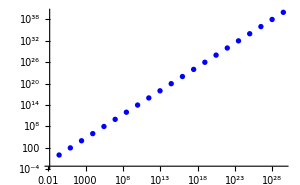

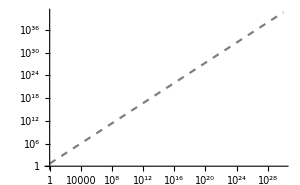

-Graphics-

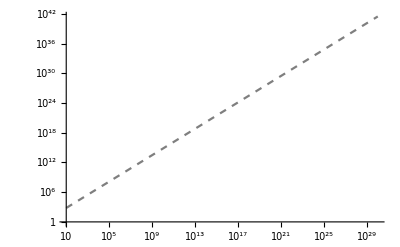

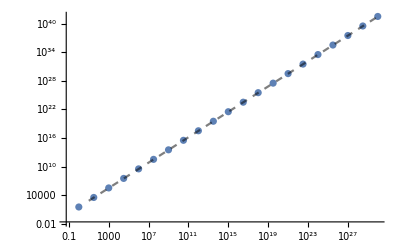

```mathematica
Qvalues =4π Table[ NIntegrate[r^2 σscaling[[i]][[1]],{r,0,Rvalues[[i]]}],{i,1,Length@zvalues}];
q3values = Table[ 2Qvalues[[i]] zvalues[[i]]^3-8π zvalues[[i]] NIntegrate[r^4 σscaling[[i]][[1]],{r,0,Rvalues[[i]]}],{i,1,Length@zvalues}];
Vvalues = Table[ σscaling[[i]][[2]]-zvalues[[i]]^3,{i,1,Length@zvalues}];
Svalues =  Table[ 2Qvalues[[i]]Vvalues[[i]]-q3values[[i]],{i,1,Length@zvalues}]
Nvalues = Table[Qvalues[[i]]zvalues[[i]],{i,1,Length@zvalues}];
dataS=Table[{Nvalues[[n]],Svalues[[n]]},{n,1,Length@zvalues}];
ListLogLogPlot[Table[{Nvalues[[n]],Svalues[[n]]},{n,1,Length@zvalues}],PlotStyle->Blue,AxesLabel->{MaTeX["N"],MaTeX["S"]},ImageSize->300]
LogLogPlot[4.78 n^(4/3),{n,1,10^30},PlotStyle->{Dashed,Opacity[0.5],Black},PlotLegends->{MaTeX["N^{4/3}"]},AxesLabel->{MaTeX["N"],MaTeX["S"]},ImageSize->300]
GraphicsRow[{Show[%%,%]}]



(*ListLogLogPlot[dataV,PlotRange->All,AxesLabel->{MaTeX["\\frac{z_s}{R_s}"],MaTeX["\\frac{1}{V_b z_s R_s^2} \\tilde{V}_s"]},
PlotStyle->Blue,ImageSize->300];*)
```

{55.066-41.3386 (-1+r/5)+6.03041 √(100-r^2)-0.274511 (50-30 r+3 r^2),113.209,0.0223823,{0.0223823,{c$28088[0]→55.066,c$28088[1]→-41.3386,c$28088[2]→-13.7255,c$28088[3]→6.03041,V0$28088→113.209}}}

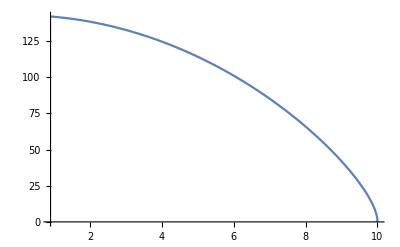

```mathematica
Rs=10;
ChargeDensity[2,Rs,1]
Plot[%[[1]],{r,0.9,Rs}]
ClearAll[Rs]
```

```mathematica
0.02382211155856836-0.017866555620740812 (-1+2 r)+6.049331540623241 √(1-r^2)-0.005955504843412408 (1-6 r+6 r^2)/.{r->1}
```

5.10944×10^-8

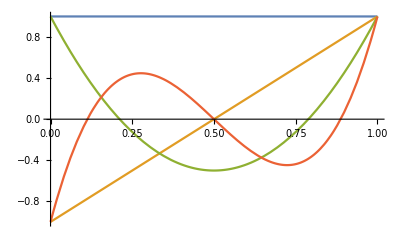

```mathematica
Table[LegendreP[n,2r-1],{n,0,3}];
Plot[%,{r,0,1}]
```

```mathematica
Integrate[r^2/(√(1-r^2)),{r,0,1}]
```

π/4

```mathematica
zvalues =10.0^Range[-3,1,4/30]
σvalues = Table[ChargeDensity[4,1,zvalues[[i]]],{i,1,Length[zvalues]}]
```

{0.001,0.00135936,0.00184785,0.00251189,0.00341455,0.00464159,0.00630957,0.00857696,0.0116591,0.0158489,0.0215443,0.0292864,0.0398107,0.054117,0.0735642,0.1,0.135936,0.184785,0.251189,0.341455,0.464159,0.630957,0.857696,1.16591,1.58489,2.15443,2.92864,3.98107,5.4117,7.35642,10.}

{{0.660825-0.496311 (-1+2 r)+0.014479 √(1-r^2)-0.164988 (1-6 r+6 r^2)+0.000380976 (-1+12 r-30 r^2+20 r^3)+0.0000939886 (1-20 r+90 r^2-140 r^3+70 r^4),0.00100381,6.95999×10^-16},{0.659208-0.495286 (-1+2 r)+0.0187976 √(1-r^2)-0.164525 (1-6 r+6 r^2)+0.000483715 (-1+12 r-30 r^2+20 r^3)+0.000119189 (1-20 r+90 r^2-140 r^3+70 r^4),0.00136609,1.74458×10^-15},{0.657167-0.49399 (-1+2 r)+0.0243793 √(1-r^2)-0.163941 (1-6 r+6 r^2)+0.00061266 (-1+12 r-30 r^2+20 r^3)+0.000150785 (1-20 r+90 r^2-140 r^3+70 r^4),0.00185975,5.14541×10^-15},{0.654593-0.492354 (-1+2 r)+0.0315891 √(1-r^2)-0.163204 (1-6 r+6 r^2)+0.00077432 (-1+12 r-30 r^2+20 r^3)+0.000190388 (1-20 r+90 r^2-140 r^3+70 r^4),0.00253287,1.40772×10^-14},{0.651354-0.490294 (-1+2 r)+0.0408991 √(1-r^2)-0.162278 (1-6 r+6 r^2)+0.000976912 (-1+12 r-30 r^2+20 r^3)+0.000240047 (1-20 r+90 r^2-140 r^3+70 r^4),0.00345147,4.07325×10^-14},{0.64728-0.4877 (-1+2 r)+0.0529228 √(1-r^2)-0.161113 (1-6 r+6 r^2)+0.00123113 (-1+12 r-30 r^2+20 r^3)+0.000302469 (1-20 r+90 r^2-140 r^3+70 r^4),0.00470643,1.17188×10^-13},{0.642151-0.484436 (-1+2 r)+0.0684649 √(1-r^2)-0.159647 (1-6 r+6 r^2)+0.00155131 (-1+12 r-30 r^2+20 r^3)+0.000381354 (1-20 r+90 r^2-140 r^3+70 r^4),0.00642315,3.31628×10^-13},{0.635676-0.480318 (-1+2 r)+0.0885922 √(1-r^2)-0.157798 (1-6 r+6 r^2)+0.00195749 (-1+12 r-30 r^2+20 r^3)+0.000481981 (1-20 r+90 r^2-140 r^3+70 r^4),0.00877531,9.35017×10^-13},{0.627455-0.475097 (-1+2 r)+0.114739 √(1-r^2)-0.155449 (1-6 r+6 r^2)+0.00247865 (-1+12 r-30 r^2+20 r^3)+0.000612146 (1-20 r+90 r^2-140 r^3+70 r^4),0.0120044,2.62628×10^-12},{0.616918-0.468423 (-1+2 r)+0.148868 √(1-r^2)-0.152437 (1-6 r+6 r^2)+0.00315795 (-1+12 r-30 r^2+20 r^3)+0.000783573 (1-20 r+90 r^2-140 r^3+70 r^4),0.0164474,7.36145×10^-12},{0.603236-0.459788 (-1+2 r)+0.193702 √(1-r^2)-0.148522 (1-6 r+6 r^2)+0.00406083 (-1+12 r-30 r^2+20 r^3)+0.00101431 (1-20 r+90 r^2-140 r^3+70 r^4),0.0225768,2.0573×10^-11},{0.585185-0.448449 (-1+2 r)+0.25306 √(1-r^2)-0.143351 (1-6 r+6 r^2)+0.00528405 (-1+12 r-30 r^2+20 r^3)+0.00133075 (1-20 r+90 r^2-140 r^3+70 r^4),0.0310575,5.68744×10^-11},{0.561013-0.43333 (-1+2 r)+0.332279 √(1-r^2)-0.136415 (1-6 r+6 r^2)+0.00696245 (-1+12 r-30 r^2+20 r^3)+0.001769 (1-20 r+90 r^2-140 r^3+70 r^4),0.0428269,1.51997×10^-10},{0.528392-0.41297 (-1+2 r)+0.438612 √(1-r^2)-0.127041 (1-6 r+6 r^2)+0.00925227 (-1+12 r-30 r^2+20 r^3)+0.00236677 (1-20 r+90 r^2-140 r^3+70 r^4),0.0592066,3.75677×10^-10},{0.484709-0.385627 (-1+2 r)+0.581379 √(1-r^2)-0.114477 (1-6 r+6 r^2)+0.0122587 (-1+12 r-30 r^2+20 r^3)+0.00313571 (1-20 r+90 r^2-140 r^3+70 r^4),0.0820458,7.97031×10^-10},{0.428009-0.349694 (-1+2 r)+0.771537 √(1-r^2)-0.0981769 (1-6 r+6 r^2)+0.0158618 (-1+12 r-30 r^2+20 r^3)+0.00400073 (1-20 r+90 r^2-140 r^3+70 r^4),0.113889,1.30201×10^-9},{0.358829-0.304588 (-1+2 r)+1.02057 √(1-r^2)-0.0783886 (1-6 r+6 r^2)+0.0194315 (-1+12 r-30 r^2+20 r^3)+0.00471663 (1-20 r+90 r^2-140 r^3+70 r^4),0.158108,1.42117×10^-9},{0.282666-0.252038 (-1+2 r)+1.33934 √(1-r^2)-0.0570092 (1-6 r+6 r^2)+0.021551 (-1+12 r-30 r^2+20 r^3)+0.00482958 (1-20 r+90 r^2-140 r^3+70 r^4),0.218846,1.01736×10^-9},{0.207038-0.195029 (-1+2 r)+1.74526 √(1-r^2)-0.0370168 (1-6 r+6 r^2)+0.0208784 (-1+12 r-30 r^2+20 r^3)+0.00412921 (1-20 r+90 r^2-140 r^3+70 r^4),0.300347,2.23386×10^-10},{0.140878-0.138504 (-1+2 r)+2.26769 √(1-r^2)-0.021918 (1-6 r+6 r^2)+0.016762 (-1+12 r-30 r^2+20 r^3)+0.00278219 (1-20 r+90 r^2-140 r^3+70 r^4),0.404527,1.25283×10^-11},{0.086692-0.0868526 (-1+2 r)+2.96402 √(1-r^2)-0.0122653 (1-6 r+6 r^2)+0.0108947 (-1+12 r-30 r^2+20 r^3)+0.00153115 (1-20 r+90 r^2-140 r^3+70 r^4),0.523913,2.35459×10^-12},{0.033865-0.0391634 (-1+2 r)+3.93165 √(1-r^2)-0.00440823 (1-6 r+6 r^2)+0.00768784 (-1+12 r-30 r^2+20 r^3)+0.00201883 (1-20 r+90 r^2-140 r^3+70 r^4),0.622688,2.45419×10^-9},{0.0208488-0.0202182 (-1+2 r)+5.22971 √(1-r^2)-0.00318499 (1-6 r+6 r^2)+0.00226291 (-1+12 r-30 r^2+20 r^3)+0.000291426 (1-20 r+90 r^2-140 r^3+70 r^4),0.587323,1.73217×10^-12},{0.00782115-0.00732257 (-1+2 r)+7.04294 √(1-r^2)-0.00130812 (1-6 r+6 r^2)+0.00071835 (-1+12 r-30 r^2+20 r^3)+0.000091189 (1-20 r+90 r^2-140 r^3+70 r^4),0.103994,3.71791×10^-12},{0.00261727-0.00230839 (-1+2 r)+9.53332 √(1-r^2)-0.000475304 (1-6 r+6 r^2)+0.000159172 (-1+12 r-30 r^2+20 r^3)+7.25477×10^-6 (1-20 r+90 r^2-140 r^3+70 r^4),-1.65344,7.65965×10^-12},{0.000983365-0.000741865 (-1+2 r)+12.9375 √(1-r^2)-0.000194403 (1-6 r+6 r^2)-0.0000195198 (-1+12 r-30 r^2+20 r^3)-0.0000275775 (1-20 r+90 r^2-140 r^3+70 r^4),-6.80774,1.5234×10^-11},{0.000629231-0.000359175 (-1+2 r)+17.5762 √(1-r^2)-0.000134086 (1-6 r+6 r^2)-0.000087674 (-1+12 r-30 r^2+20 r^3)-0.0000482962 (1-20 r+90 r^2-140 r^3+70 r^4),-20.7562,2.91038×10^-11},{0.00068335-0.000329904 (-1+2 r)+23.8876 √(1-r^2)-0.000149868 (1-6 r+6 r^2)-0.000134717 (-1+12 r-30 r^2+20 r^3)-0.0000688602 (1-20 r+90 r^2-140 r^3+70 r^4),-57.147,5.45697×10^-11},{0.000892438-0.000413258 (-1+2 r)+32.4698 √(1-r^2)-0.000196872 (1-6 r+6 r^2)-0.000187527 (-1+12 r-30 r^2+20 r^3)-0.0000947806 (1-20 r+90 r^2-140 r^3+70 r^4),-150.389,1.74623×10^-10},{0.00120783-0.000555123 (-1+2 r)+44.1372 √(1-r^2)-0.00026672 (1-6 r+6 r^2)-0.000256556 (-1+12 r-30 r^2+20 r^3)-0.00012943 (1-20 r+90 r^2-140 r^3+70 r^4),-387.085,2.32831×10^-10},{0.00164285-0.000754081 (-1+2 r)+59.9978 √(1-r^2)-0.000362853 (1-6 r+6 r^2)-0.000349601 (-1+12 r-30 r^2+20 r^3)-0.000176313 (1-20 r+90 r^2-140 r^3+70 r^4),-985.009,0.}}

```mathematica
zvalues =10.0^Range[-3,1,4/30];
σvalues = {{0.6608246059028463-0.49631117115205525 (-1+2 r)+0.014478981894818525 √(1-r^2)-0.16498839961699568 (1-6 r+6 r^2)+0.0003809763102862827 (-1+12 r-30 r^2+20 r^3)+0.00009398855607852983 (1-20 r+90 r^2-140 r^3+70 r^4),0.001003807377482264,6.959989259458597*^-16},{0.6592084136470645-0.4952860891927837 (-1+2 r)+0.01879762052023725 √(1-r^2)-0.16452522870011393 (1-6 r+6 r^2)+0.0004837153471388923 (-1+12 r-30 r^2+20 r^3)+0.00011918889907058374 (1-20 r+90 r^2-140 r^3+70 r^4),0.0013660920682746047,1.7445795513510581*^-15},{0.657166983434534-0.49398984901856247 (-1+2 r)+0.02437925463087217 √(1-r^2)-0.16394058036163411 (1-6 r+6 r^2)+0.000612660462401582 (-1+12 r-30 r^2+20 r^3)+0.00015078548414729814 (1-20 r+90 r^2-140 r^3+70 r^4),0.0018597476671440502,5.145410058313496*^-15},{0.6545934285076586-0.4923541126951945 (-1+2 r)+0.03158911384175293 √(1-r^2)-0.16320402395318398 (1-6 r+6 r^2)+0.0007743201413728849 (-1+12 r-30 r^2+20 r^3)+0.00019038800142505305 (1-20 r+90 r^2-140 r^3+70 r^4),0.0025328667405686268,1.4077248820299794*^-14},{0.6513541436763238-0.4902935776405576 (-1+2 r)+0.04089908985274028 √(1-r^2)-0.16227752551892846 (1-6 r+6 r^2)+0.0009769122475118356 (-1+12 r-30 r^2+20 r^3)+0.000240047240506324 (1-20 r+90 r^2-140 r^3+70 r^4),0.0034514731543053645,4.0732499838325165*^-14},{0.647279647249861-0.48770044638046245 (-1+2 r)+0.05292284563853076 √(1-r^2)-0.1611127953084624 (1-6 r+6 r^2)+0.0012311253093985526 (-1+12 r-30 r^2+20 r^3)+0.00030246914098087496 (1-20 r+90 r^2-140 r^3+70 r^4),0.0047064300274482105,1.171882618613944*^-13},{0.6421506902207755-0.4844361009058345 (-1+2 r)+0.0684649398205314 √(1-r^2)-0.15964725539831562 (1-6 r+6 r^2)+0.0015513122367792232 (-1+12 r-30 r^2+20 r^3)+0.0003813538728781361 (1-20 r+90 r^2-140 r^3+70 r^4),0.006423148988882815,3.3162781873895264*^-13},{0.6356758093674404-0.4803177541317863 (-1+2 r)+0.08859221485672601 √(1-r^2)-0.15779753099275576 (1-6 r+6 r^2)+0.0019574949556669112 (-1+12 r-30 r^2+20 r^3)+0.00048198086225439133 (1-20 r+90 r^2-140 r^3+70 r^4),0.008775312503708856,9.350174985395948*^-13},{0.6274547301839661-0.4750967494328513 (-1+2 r)+0.1147393042106079 √(1-r^2)-0.15544877365307788 (1-6 r+6 r^2)+0.0024786474251327338 (-1+12 r-30 r^2+20 r^3)+0.0006121456169255873 (1-20 r+90 r^2-140 r^3+70 r^4),0.012004371591429473,2.6262809201677006*^-12},{0.6169184078809596-0.4684229295537378 (-1+2 r)+0.1488676511087417 √(1-r^2)-0.1524369969210576 (1-6 r+6 r^2)+0.0031579454833109448 (-1+12 r-30 r^2+20 r^3)+0.0007835734307799092 (1-20 r+90 r^2-140 r^3+70 r^4),0.01644737784554986,7.361454328058681*^-12},{0.6032355185299716-0.45978845198824575 (-1+2 r)+0.1937018873249417 √(1-r^2)-0.1485222042930545 (1-6 r+6 r^2)+0.004060826464417351 (-1+12 r-30 r^2+20 r^3)+0.0010143120097023746 (1-20 r+90 r^2-140 r^3+70 r^4),0.02257680904156734,2.0573040883722915*^-11},{0.5851854876565585-0.44844942114632175 (-1+2 r)+0.2530595827577119 √(1-r^2)-0.14335085916677084 (1-6 r+6 r^2)+0.005284049079521204 (-1+12 r-30 r^2+20 r^3)+0.001330745169300228 (1-20 r+90 r^2-140 r^3+70 r^4),0.03105746258096722,5.687439473371636*^-11},{0.5610130410275264-0.4333295499689754 (-1+2 r)+0.33227865373045673 √(1-r^2)-0.13641493836377094 (1-6 r+6 r^2)+0.006962452481373332 (-1+12 r-30 r^2+20 r^3)+0.0017689981700895658 (1-20 r+90 r^2-140 r^3+70 r^4),0.04282694025251052,1.5199744284391525*^-10},{0.5283920632993933-0.41296978964742254 (-1+2 r)+0.4386123798634747 √(1-r^2)-0.1270413045426501 (1-6 r+6 r^2)+0.009252265408801643 (-1+12 r-30 r^2+20 r^3)+0.0023667719514524504 (1-20 r+90 r^2-140 r^3+70 r^4),0.059206561573353134,3.756770528343112*^-10},{0.4847094352723358-0.38562667803398387 (-1+2 r)+0.5813790152060818 √(1-r^2)-0.11447717664158612 (1-6 r+6 r^2)+0.01225871540392643 (-1+12 r-30 r^2+20 r^3)+0.003135714933076111 (1-20 r+90 r^2-140 r^3+70 r^4),0.08204584339019559,7.970310626770338*^-10},{0.42800853765534735-0.34969411191747496 (-1+2 r)+0.7715373339039029 √(1-r^2)-0.09817690892404542 (1-6 r+6 r^2)+0.015861772625768548 (-1+12 r-30 r^2+20 r^3)+0.00400072575360295 (1-20 r+90 r^2-140 r^3+70 r^4),0.11388883229843544,1.3020073907910046*^-9},{0.3588287372700419-0.30458828617794814 (-1+2 r)+1.020572691065374 √(1-r^2)-0.07838855265659002 (1-6 r+6 r^2)+0.019431487451550867 (-1+12 r-30 r^2+20 r^3)+0.004716630412059671 (1-20 r+90 r^2-140 r^3+70 r^4),0.15810842962933647,1.4211684051801399*^-9},{0.2826662871900057-0.2520377187376857 (-1+2 r)+1.3393388543465243 √(1-r^2)-0.05700915114216655 (1-6 r+6 r^2)+0.021551013887769123 (-1+12 r-30 r^2+20 r^3)+0.004829582494821082 (1-20 r+90 r^2-140 r^3+70 r^4),0.21884566080748497,1.0173630132781497*^-9},{0.20703811679856549-0.19502891033924227 (-1+2 r)+1.745257208618787 √(1-r^2)-0.03701682757848985 (1-6 r+6 r^2)+0.02087841865901247 (-1+12 r-30 r^2+20 r^3)+0.004129208757187995 (1-20 r+90 r^2-140 r^3+70 r^4),0.3003473062079935,2.2338569882762727*^-10},{0.14087778966029332-0.13850395051541406 (-1+2 r)+2.2676948470774074 √(1-r^2)-0.02191799691292905 (1-6 r+6 r^2)+0.01676197195268354 (-1+12 r-30 r^2+20 r^3)+0.002782187272194002 (1-20 r+90 r^2-140 r^3+70 r^4),0.4045265937129721,1.2528311721382579*^-11},{0.08669195013511242-0.08685257594455505 (-1+2 r)+2.964016097849778 √(1-r^2)-0.012265255093220646 (1-6 r+6 r^2)+0.010894725967568344 (-1+12 r-30 r^2+20 r^3)+0.0015311544812373042 (1-20 r+90 r^2-140 r^3+70 r^4),0.5239134867862602,2.3545887462006476*^-12},{0.03386496076040366-0.03916341388036155 (-1+2 r)+3.9316502393715322 √(1-r^2)-0.004408227132771845 (1-6 r+6 r^2)+0.0076878389589116304 (-1+12 r-30 r^2+20 r^3)+0.00201882904727366 (1-20 r+90 r^2-140 r^3+70 r^4),0.6226877404466987,2.454193237522162*^-9},{0.020848821291775812-0.02021816552808493 (-1+2 r)+5.229711145488745 √(1-r^2)-0.0031849907427745064 (1-6 r+6 r^2)+0.0022629089878865257 (-1+12 r-30 r^2+20 r^3)+0.000291426054938348 (1-20 r+90 r^2-140 r^3+70 r^4),0.587323334805843,1.7321699630201692*^-12},{0.007821152201108171-0.007322570955649225 (-1+2 r)+7.0429437584802 √(1-r^2)-0.001308120170615281 (1-6 r+6 r^2)+0.0007183500755823233 (-1+12 r-30 r^2+20 r^3)+0.00009118899288153618 (1-20 r+90 r^2-140 r^3+70 r^4),0.10399363964889737,3.717914864864724*^-12},{0.002617271257742806-0.0023083937333361654 (-1+2 r)+9.533320714395863 √(1-r^2)-0.00047530382640647163 (1-6 r+6 r^2)+0.0001591716873804128 (-1+12 r-30 r^2+20 r^3)+7.254773263429122*^-6 (1-20 r+90 r^2-140 r^3+70 r^4),-1.6534391008755418,7.65965069149388*^-12},{0.0009833653540341934-0.0007418649794995032 (-1+2 r)+12.937450868885177 √(1-r^2)-0.00019440286947065537 (1-6 r+6 r^2)-0.00001951978476143987 (-1+12 r-30 r^2+20 r^3)-0.000027577528912448358 (1-20 r+90 r^2-140 r^3+70 r^4),-6.807736252683114,1.5234036254696548*^-11},{0.0006292309165008246-0.00035917470529492503 (-1+2 r)+17.57615287844477 √(1-r^2)-0.00013408570282767823 (1-6 r+6 r^2)-0.00008767404068353488 (-1+12 r-30 r^2+20 r^3)-0.00004829621377702594 (1-20 r+90 r^2-140 r^3+70 r^4),-20.756177035607642,2.9103830456733704*^-11},{0.0006833501217388099-0.0003299038278380164 (-1+2 r)+23.887591607426067 √(1-r^2)-0.00014986848882107324 (1-6 r+6 r^2)-0.00013471723869874002 (-1+12 r-30 r^2+20 r^3)-0.00006886022038348281 (1-20 r+90 r^2-140 r^3+70 r^4),-57.14697089258967,5.4569682106375694*^-11},{0.0008924383954980453-0.0004132578502057559 (-1+2 r)+32.469765391687865 √(1-r^2)-0.0001968721857018895 (1-6 r+6 r^2)-0.0001875273133386487 (-1+12 r-30 r^2+20 r^3)-0.00009478057351318151 (1-20 r+90 r^2-140 r^3+70 r^4),-150.38882354907466,1.7462298274040222*^-10},{0.0012078297621452446-0.0005551229184829554 (-1+2 r)+44.13716093602273 √(1-r^2)-0.0002667198224637722 (1-6 r+6 r^2)-0.0002565562215398389 (-1+12 r-30 r^2+20 r^3)-0.00012943015472867856 (1-20 r+90 r^2-140 r^3+70 r^4),-387.0851822601704,2.3283064365386963*^-10},{0.0016428486779301575-0.0007540811373769796 (-1+2 r)+59.997795883241835 √(1-r^2)-0.00036285348332616983 (1-6 r+6 r^2)-0.00034960062914460023 (-1+12 r-30 r^2+20 r^3)-0.00017631255069903314 (1-20 r+90 r^2-140 r^3+70 r^4),-985.0093528844016,0.}};
```

```mathematica
Qvalues =4π Table[ NIntegrate[r^2 σvalues[[i]][[1]],{r,0,1}],{i,1,Length[zvalues]}]
Vvalues = Table[ σvalues[[i]][[2]],{i,1,Length[zvalues]}]
q3values = Table[ 2Qvalues[[i]] zvalues[[i]]^3-8π zvalues[[i]] NIntegrate[r^4 σvalues[[i]][[1]],{r,0,1}],{i,1,Length@zvalues}]
ξvalues = Table[(243 Qvalues[[i]])/(1048576 π^2 zvalues[[i]]^5),{i,1,Length@zvalues}]
Svalues = Table[(9  (243 35/(16 π zvalues[[i]])q3values[[i]]+4587520 π zvalues[[i]]^5 ((-Vvalues[[i]])/zvalues[[i]]-zvalues[[i]]^2+zvalues[[i]]^2) ξvalues[[i]]))/(300647710720 π zvalues[[i]]^7  ξvalues[[i]]^(4/3)),{i,1,Length@zvalues}]
```

{1.6952,1.70143,1.70961,1.72035,1.73446,1.75298,1.77729,1.80923,1.85123,1.90654,1.97958,2.07634,2.20513,2.37742,2.60923,2.92301,3.35046,3.93697,4.74952,5.88616,7.48951,9.75894,12.9474,17.3946,23.5285,31.9244,43.3692,58.9424,80.1187,108.908,148.044}

{0.00100381,0.00136609,0.00185975,0.00253287,0.00345147,0.00470643,0.00642315,0.00877531,0.0120044,0.0164474,0.0225768,0.0310575,0.0428269,0.0592066,0.0820458,0.113889,0.158108,0.218846,0.300347,0.404527,0.523913,0.622688,0.587323,0.103994,-1.65344,-6.80774,-20.7562,-57.147,-150.389,-387.085,-985.009}

{-0.00145743,-0.00199022,-0.00272157,-0.00372832,-0.00511927,-0.00704992,-0.00974528,-0.0135355,-0.0189127,-0.0266241,-0.037826,-0.0543442,-0.0791194,-0.116968,-0.175858,-0.268966,-0.417582,-0.653794,-1.01695,-1.51654,-1.95752,-1.24062,5.24248,34.861,150.049,569.709,2051.76,7203.37,24962.3,85912.8,294607.}

{3.98041×10^10,8.60702×10^9,1.86324×10^9,4.03946×10^8,8.77412×10^7,1.91051×10^7,4.17316×10^6,915238.,201759.,44766.5,10014.1,2262.94,517.774,120.267,28.4372,6.86336,1.6949,0.429077,0.111521,0.0297764,0.00816257,0.00229144,0.000654974,0.000189578,0.0000552459,0.0000161496,4.72667×10^-6,1.38399×10^-6,4.05298×10^-7,1.18695×10^-7,3.47614×10^-8}

{-0.057664,-0.0520467,-0.0469736,-0.0423908,-0.0382499,-0.0345069,-0.0311216,-0.0280575,-0.0252813,-0.022762,-0.0204714,-0.0183827,-0.0164708,-0.0147115,-0.0130809,-0.0115547,-0.0101075,-0.00871129,-0.00733394,-0.00593586,-0.00446473,-0.00284583,-0.000964576,0.00135459,0.00438561,0.00854644,0.0144677,0.0230955,0.0358485,0.0548557,0.0833165}

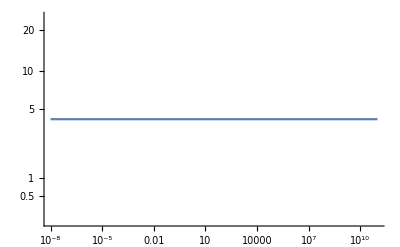

```mathematica
dataS=Table[{ξvalues[[n]],Svalues[[n]]},{n,1,Length@zvalues}];
symlog={Function[x,Sign[x]*Log[Abs[x]+1]],Function[y,Sign[y]*(Exp[Abs[y]]-1)]};
ListLogLinearPlot[%%,ScalingFunctions->symlog,AxesLabel->{MaTeX["\\xi"], MaTeX["- \\frac{ \\lambda^{2/3}}{N^2}S_\\mathrm{on-shell}"]},PlotStyle->Blue,ImageSize->300];
LogLinearPlot[-5/(7 2^7)(15 π/8)^(2/5)ξ^(1/15),{ξ,0.01,10^11},ScalingFunctions->symlog,PlotStyle->{Dashed, Black},ImageSize->300];
LogLinearPlot[{-1000000,9/2^15 ξ^(-1/3)},{ξ,10^-8,10^1},ScalingFunctions->symlog,PlotStyle->{{Dashed, Black},{Dashed, Red}},PlotLegends->Placed[LineLegend[{MaTeX["H(\\xi) = -\\frac{5}{7\\, 2^7} (15 \\pi/8)^{2/5}  \\xi^{1/15}"],MaTeX["H(\\xi) = \\frac{9}{2^{15}}\\xi^{-1/3}"]},LegendLayout->{"Column",1},LegendMarkerSize->16],{0.95,0.8},Pane[#,300,Alignment->Left]&],ImageSize->300];
LogLinearPlot[3^(7/3)/2^(5/3),{ξ,10^-8,10^11},ScalingFunctions->symlog]
GraphicsRow[{Show[%%%%,%%%,%%,%]}]
```

```mathematica
Solve[9/2^15 ξ^(-1/3)==3^(7/3)/2^(5/3),ξ]
FactorInteger[3298534883328]
```

{{ξ→1/3298534883328}}

{{2,40},{3,1}}

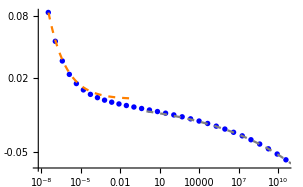

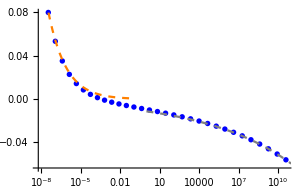

{{0.001,1.01175},{0.00135936,1.01546},{0.00184785,1.02035},{0.00251189,1.02676},{0.00341455,1.03518},{0.00464159,1.04623},{0.00630957,1.06074},{0.00857696,1.07981},{0.0116591,1.10487},{0.0158489,1.13788},{0.0215443,1.18147},{0.0292864,1.23923},{0.0398107,1.31609},{0.054117,1.41892},{0.0735642,1.55727},{0.1,1.74454},{0.135936,1.99966},{0.184785,2.34971},{0.251189,2.83466},{0.341455,3.51304},{0.464159,4.46997},{0.630957,5.82444},{0.857696,7.72744},{1.16591,10.3817},{1.58489,14.0425},{2.15443,19.0535},{2.92864,25.8841},{3.98107,35.1786},{5.4117,47.8173},{7.35642,64.9996},{10.,88.3571}}

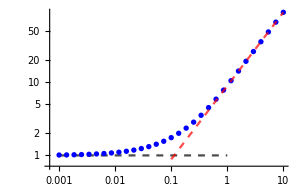

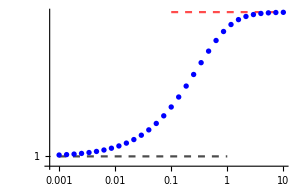

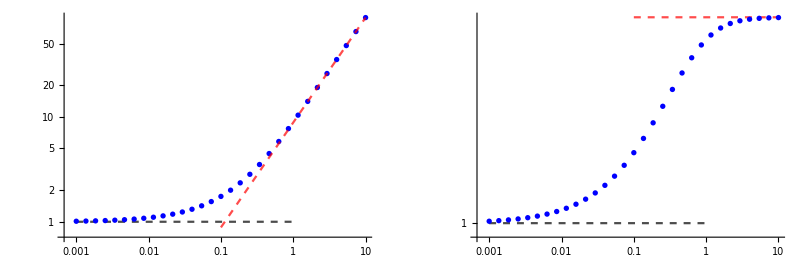

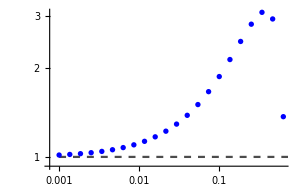

```mathematica
dataQ=Table[{zvalues[[n]],Qvalues[[n]]/(8/15 π)},{n,1,Length@zvalues}]
ListLogLogPlot[dataQ,PlotRange->All,
AxesLabel->{MaTeX["\\frac{z_s}{R_s}"],MaTeX[" \\frac{15}{8 \\pi V_b R_s^5} Q_s"]},
PlotStyle->Blue,ImageSize->300
];
LogLogPlot[ 1,{z,1/1000,1},PlotStyle->{Dashed,Black,Opacity[0.7]},ImageSize->300];
LogLogPlot[{-10000,1/(8/15 π) 3/2 π^2 z},{z,1/10,10},PlotStyle->{{Dashed,Black,Opacity[0.7]},{Dashed,Red,Opacity[0.7]}},ImageSize->300,
PlotLegends->Placed[LineLegend[{MaTeX["Q_s = \\frac{8 \\pi}{15} V_b R_s^5"],MaTeX["Q_s = \\frac{3 \\pi^2}{2} V_b R_s^4 z_s"]},LegendLayout->{"Column",1},LegendMarkerSize->16],{0.99,0.7},Pane[#,450,Alignment->Left]&]];
a=Show[%%%,%%,%]
dataV=Table[{zvalues[[n]],(Vvalues[[n]]+zvalues[[n]]^3)/zvalues[[n]]},{n,1,Length@zvalues}];
ListLogLogPlot[dataV,PlotRange->All,AxesLabel->{MaTeX["\\frac{z_s}{R_s}"],MaTeX["\\frac{1}{V_b z_s R_s^2} \\tilde{V}_s"]},
PlotStyle->Blue,ImageSize->300];
LogLogPlot[ 1,{z,1/1000,1},PlotStyle->{Dashed,Black,Opacity[0.7]},ImageSize->300];
LogLogPlot[{-10000,3/2},{z,1/10,10},PlotStyle->{{Dashed,Black,Opacity[0.7]},{Dashed,Red,Opacity[0.7]}},
PlotLegends->Placed[LineLegend[{MaTeX["\\tilde{V}_s = V_b z_sR_s^2"],MaTeX["\\tilde{V}_s = \\frac{3}{2} V_b z_sR_s^2"]},LegendLayout->{"Column",1},LegendMarkerSize->16],{0.99,0.7},Pane[#,450,Alignment->Left]&], 
(*PlotLegends->{MaTeX["\\tilde{V}_s = V_b z_sR_s^2, \\quad Q_s = \\frac{8 \\pi}{15} V_b R_s^5 "],MaTeX["\\tilde{V}_s = \\frac{3}{2} V_b z_sR_s^2, \\quad Q_s = \\frac{3 \\pi^2}{2} V_b R_s^4 z_s "]}*)ImageSize->300];
b=Show[%%%,%%,%]
GraphicsRow[{a,b}]
dataq3=Table[{zvalues[[n]],q3values[[n]]/(-(16 π)/35 zvalues[[n]])},{n,1,Length@zvalues}];
ListLogLogPlot[dataq3,PlotRange->All,
AxesLabel->{MaTeX["\\frac{z_s}{R_s}"],MaTeX[" -\\frac{35}{16 \\pi V_b R_s^7} q_{3,s}"]},
PlotStyle->Blue,ImageSize->300
];
LogLogPlot[ 1,{z,1/1000,1},PlotStyle->{Dashed,Black,Opacity[0.7]},ImageSize->300];
LogLogPlot[{-10000,1/(-16/35 π)  z},{z,1/10,10},PlotStyle->{{Dashed,Black,Opacity[0.7]},{Dashed,Red,Opacity[0.7]}},ImageSize->300,
PlotLegends->Placed[LineLegend[{MaTeX["Q_s = \\frac{8 \\pi}{15} V_b R_s^5"],MaTeX["Q_s = \\frac{3 \\pi^2}{2} V_b R_s^4 z_s"]},LegendLayout->{"Column",1},LegendMarkerSize->16],{0.99,0.7},Pane[#,450,Alignment->Left]&]];
a=Show[%%%,%%,%]
```

{{0.001,-1.01481},{0.00135936,-1.01945},{0.00184785,-1.02554},{0.00251189,-1.0335},{0.00341455,-1.04393},{0.00464159,-1.05759},{0.00630957,-1.07546},{0.00857696,-1.09885},{0.0116591,-1.1295},{0.0158489,-1.1697},{0.0215443,-1.22252},{0.0292864,-1.29207},{0.0398107,-1.38383},{0.054117,-1.50498},{0.0735642,-1.66454},{0.1,-1.87282},{0.135936,-2.13898},{0.184785,-2.46361},{0.251189,-2.81901},{0.341455,-3.09257},{0.464159,-2.93656},{0.630957,-1.3691},{0.857696,4.256},{1.16591,20.8195},{1.58489,65.922},{2.15443,184.127},{2.92864,487.818},{3.98107,1259.89},{5.4117,3211.81},{7.35642,8131.85},{10.,20513.6}}

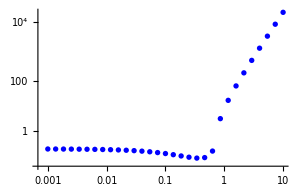

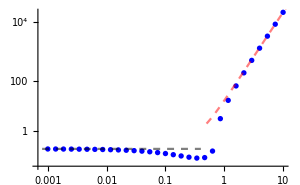

```mathematica
Qvalues =4π Table[ NIntegrate[r^2 σvalues[[i]][[1]],{r,0,1}],{i,1,Length[zvalues]}];
q3values = Table[ 2Qvalues[[i]] zvalues[[i]]^3-8π zvalues[[i]] NIntegrate[r^4 σvalues[[i]][[1]],{r,0,1}],{i,1,Length@zvalues}];
dataq3=Table[{zvalues[[n]],q3values[[n]]/(16 π/35 zvalues[[n]])},{n,1,Length@zvalues}];
q= 3/2 π^2 z;

symlog={Function[x,Sign[x]*Log[Abs[x]+1]],Function[y,Sign[y]*(Exp[Abs[y]]-1)]};

ListLogLinearPlot[dataq3,PlotRange->All, ScalingFunctions->symlog,
AxesLabel->{MaTeX["\\frac{z_s}{R_s}"],MaTeX[" \\frac{35}{16 \\pi V_b R_s^7 z_s} q_{3,s}"]},
PlotStyle->Blue,ImageSize->300
]
LogLinearPlot[ -1,{z,0.8/1000,4/10}, ScalingFunctions->symlog,PlotStyle->{Dashed,Black,Opacity[0.5]},ImageSize->300];
LogLinearPlot[{-10000,1/(16/35 π z)  ((2q z^3))},{z,0.5,11}, ScalingFunctions->symlog,PlotStyle->{{Dashed,Black,Opacity[0.5]},{Dashed,Red,Opacity[0.5]}},ImageSize->300,PlotLegends->Placed[LineLegend[{MaTeX["q_{3,s} = -\\frac{16\\pi}{35} V_b R_s^7 z_s"],MaTeX["q_{3,s} = 2 Q_s z_s^3"]},LegendLayout->{"Column",1},LegendMarkerSize->16],{0.99,0.7},Pane[#,450,Alignment->Left]&]];
a=GraphicsRow[{Show[%%%,%%,%]}]

(*Qvalueszoom =4π Table[ NIntegrate[r^2 σvalueszoom[[i]][[1]],{r,0,1}],{i,1,Length[zvalueszoom]}];
q3valueszoom = Table[ 2Qvalueszoom[[i]] zvalueszoom[[i]]^3-8π zvalueszoom[[i]] NIntegrate[r^4 σvalueszoom[[i]][[1]],{r,0,1}],{i,1,Length@zvalueszoom}];

dataq3zoom=Table[{zvalueszoom[[n]],q3valueszoom[[n]]/(16 π/35 zvalueszoom[[n]])+5},{n,1,Length@zvalueszoom}];
ListLogLogPlot[dataq3zoom,PlotRange->All,
AxesLabel->{MaTeX["\\frac{z_s}{R_s}"],MaTeX[" \\frac{35}{16 \\pi V_b R_s^7} q_{3,s}"]},
PlotStyle->Blue,ImageSize->300
];
b=Show[%]*)
```

```mathematica
zvalueszoom =10.0^Range[-1,0,1/30]
σvalueszoom = Table[ChargeDensity[4,1,zvalues[[i]]],{i,1,Length[zvalues]}]
```

{0.1,0.107978,0.116591,0.125893,0.135936,0.14678,0.158489,0.171133,0.184785,0.199526,0.215443,0.232631,0.251189,0.271227,0.292864,0.316228,0.341455,0.368695,0.398107,0.429866,0.464159,0.501187,0.54117,0.584341,0.630957,0.681292,0.735642,0.794328,0.857696,0.926119,1.}

{{0.428009-0.349694 (-1+2 r)+0.771537 √(1-r^2)-0.0981769 (1-6 r+6 r^2)+0.0158618 (-1+12 r-30 r^2+20 r^3)+0.00400073 (1-20 r+90 r^2-140 r^3+70 r^4),0.113889,1.30201×10^-9,{1.30201×10^-9,{c$365060[0]→0.428009,c$365060[1]→-0.349694,c$365060[2]→-0.0981769,c$365060[3]→0.0158618,c$365060[4]→0.00400073,c$365060[5]→0.771537,V0$365060→0.113889}}},{0.411774-0.339261 (-1+2 r)+0.827834 √(1-r^2)-0.0935184 (1-6 r+6 r^2)+0.0167975 (-1+12 r-30 r^2+20 r^3)+0.00420788 (1-20 r+90 r^2-140 r^3+70 r^4),0.123633,1.39088×10^-9,{1.39088×10^-9,{c$391741[0]→0.411774,c$391741[1]→-0.339261,c$391741[2]→-0.0935184,c$391741[3]→0.0167975,c$391741[4]→0.00420788,c$391741[5]→0.827834,V0$391741→0.123633}}},{0.394784-0.328253 (-1+2 r)+0.88799 √(1-r^2)-0.0886506 (1-6 r+6 r^2)+0.0177181 (-1+12 r-30 r^2+20 r^3)+0.00440082 (1-20 r+90 r^2-140 r^3+70 r^4),0.134207,1.44534×10^-9,{1.44534×10^-9,{c$418422[0]→0.394784,c$418422[1]→-0.328253,c$418422[2]→-0.0886506,c$418422[3]→0.0177181,c$418422[4]→0.00440082,c$418422[5]→0.88799,V0$418422→0.134207}}},{0.377106-0.316686 (-1+2 r)+0.952178 √(1-r^2)-0.083597 (1-6 r+6 r^2)+0.0186038 (-1+12 r-30 r^2+20 r^3)+0.00457282 (1-20 r+90 r^2-140 r^3+70 r^4),0.145677,1.45717×10^-9,{1.45717×10^-9,{c$445103[0]→0.377106,c$445103[1]→-0.316686,c$445103[2]→-0.083597,c$445103[3]→0.0186038,c$445103[4]→0.00457282,c$445103[5]→0.952178,V0$445103→0.145677}}},{0.358829-0.304588 (-1+2 r)+1.02057 √(1-r^2)-0.0783886 (1-6 r+6 r^2)+0.0194315 (-1+12 r-30 r^2+20 r^3)+0.00471663 (1-20 r+90 r^2-140 r^3+70 r^4),0.158108,1.42117×10^-9,{1.42117×10^-9,{c$471784[0]→0.358829,c$471784[1]→-0.304588,c$471784[2]→-0.0783886,c$471784[3]→0.0194315,c$471784[4]→0.00471663,c$471784[5]→1.02057,V0$471784→0.158108}}},{0.340063-0.291999 (-1+2 r)+1.09335 √(1-r^2)-0.0730642 (1-6 r+6 r^2)+0.0201756 (-1+12 r-30 r^2+20 r^3)+0.00482471 (1-20 r+90 r^2-140 r^3+70 r^4),0.171571,1.33668×10^-9,{1.33668×10^-9,{c$498465[0]→0.340063,c$498465[1]→-0.291999,c$498465[2]→-0.0730642,c$498465[3]→0.0201756,c$498465[4]→0.00482471,c$498465[5]→1.09335,V0$498465→0.171571}}},{0.320914-0.278955 (-1+2 r)+1.17073 √(1-r^2)-0.0676635 (1-6 r+6 r^2)+0.0208133 (-1+12 r-30 r^2+20 r^3)+0.00489148 (1-20 r+90 r^2-140 r^3+70 r^4),0.186135,1.19982×10^-9,{1.19982×10^-9,{c$525146[0]→0.320914,c$525146[1]→-0.278955,c$525146[2]→-0.0676635,c$525146[3]→0.0208133,c$525146[4]→0.00489148,c$525146[5]→1.17073,V0$525146→0.186135}}},{0.301985-0.265738 (-1+2 r)+1.25231 √(1-r^2)-0.0623582 (1-6 r+6 r^2)+0.0212364 (-1+12 r-30 r^2+20 r^3)+0.00487545 (1-20 r+90 r^2-140 r^3+70 r^4),0.201869,1.17831×10^-9,{1.17831×10^-9,{c$551827[0]→0.301985,c$551827[1]→-0.265738,c$551827[2]→-0.0623582,c$551827[3]→0.0212364,c$551827[4]→0.00487545,c$551827[5]→1.25231,V0$551827→0.201869}}},{0.282666-0.252038 (-1+2 r)+1.33934 √(1-r^2)-0.0570092 (1-6 r+6 r^2)+0.021551 (-1+12 r-30 r^2+20 r^3)+0.00482958 (1-20 r+90 r^2-140 r^3+70 r^4),0.218846,1.01736×10^-9,{1.01736×10^-9,{c$578508[0]→0.282666,c$578508[1]→-0.252038,c$578508[2]→-0.0570092,c$578508[3]→0.021551,c$578508[4]→0.00482958,c$578508[5]→1.33934,V0$578508→0.218846}}},{0.262932-0.237836 (-1+2 r)+1.43236 √(1-r^2)-0.0516234 (1-6 r+6 r^2)+0.0217653 (-1+12 r-30 r^2+20 r^3)+0.0047626 (1-20 r+90 r^2-140 r^3+70 r^4),0.237131,6.76843×10^-10,{6.76843×10^-10,{c$605189[0]→0.262932,c$605189[1]→-0.237836,c$605189[2]→-0.0516234,c$605189[3]→0.0217653,c$605189[4]→0.0047626,c$605189[5]→1.43236,V0$605189→0.237131}}},{0.243878-0.22366 (-1+2 r)+1.53043 √(1-r^2)-0.0465177 (1-6 r+6 r^2)+0.0216936 (-1+12 r-30 r^2+20 r^3)+0.00460553 (1-20 r+90 r^2-140 r^3+70 r^4),0.256779,5.00538×10^-10,{5.00538×10^-10,{c$631870[0]→0.243878,c$631870[1]→-0.22366,c$631870[2]→-0.0465177,c$631870[3]→0.0216936,c$631870[4]→0.00460553,c$631870[5]→1.53043,V0$631870→0.256779}}},{0.225208-0.209368 (-1+2 r)+1.63456 √(1-r^2)-0.0416318 (1-6 r+6 r^2)+0.0213996 (-1+12 r-30 r^2+20 r^3)+0.00439246 (1-20 r+90 r^2-140 r^3+70 r^4),0.27784,3.46952×10^-10,{3.46952×10^-10,{c$658551[0]→0.225208,c$658551[1]→-0.209368,c$658551[2]→-0.0416318,c$658551[3]→0.0213996,c$658551[4]→0.00439246,c$658551[5]→1.63456,V0$658551→0.27784}}},{0.207038-0.195029 (-1+2 r)+1.74526 √(1-r^2)-0.0370168 (1-6 r+6 r^2)+0.0208784 (-1+12 r-30 r^2+20 r^3)+0.00412921 (1-20 r+90 r^2-140 r^3+70 r^4),0.300347,2.23386×10^-10,{2.23386×10^-10,{c$685232[0]→0.207038,c$685232[1]→-0.195029,c$685232[2]→-0.0370168,c$685232[3]→0.0208784,c$685232[4]→0.00412921,c$685232[5]→1.74526,V0$685232→0.300347}}},{0.189461-0.180707 (-1+2 r)+1.86314 √(1-r^2)-0.0327143 (1-6 r+6 r^2)+0.0201352 (-1+12 r-30 r^2+20 r^3)+0.0038247 (1-20 r+90 r^2-140 r^3+70 r^4),0.324311,1.31976×10^-10,{1.31976×10^-10,{c$711913[0]→0.189461,c$711913[1]→-0.180707,c$711913[2]→-0.0327143,c$711913[3]→0.0201352,c$711913[4]→0.0038247,c$711913[5]→1.86314,V0$711913→0.324311}}},{0.172547-0.166467 (-1+2 r)+1.98894 √(1-r^2)-0.0287545 (1-6 r+6 r^2)+0.0191842 (-1+12 r-30 r^2+20 r^3)+0.00349018 (1-20 r+90 r^2-140 r^3+70 r^4),0.349711,7.02325×10^-11,{7.02325×10^-11,{c$738594[0]→0.172547,c$738594[1]→-0.166467,c$738594[2]→-0.0287545,c$738594[3]→0.0191842,c$738594[4]→0.00349018,c$738594[5]→1.98894,V0$738594→0.349711}}},{0.156297-0.152354 (-1+2 r)+2.12353 √(1-r^2)-0.0251421 (1-6 r+6 r^2)+0.0180574 (-1+12 r-30 r^2+20 r^3)+0.00314169 (1-20 r+90 r^2-140 r^3+70 r^4),0.376489,2.95645×10^-11,{2.95645×10^-11,{c$765275[0]→0.156297,c$765275[1]→-0.152354,c$765275[2]→-0.0251421,c$765275[3]→0.0180574,c$765275[4]→0.00314169,c$765275[5]→2.12353,V0$765275→0.376489}}},{0.140878-0.138504 (-1+2 r)+2.26769 √(1-r^2)-0.021918 (1-6 r+6 r^2)+0.016762 (-1+12 r-30 r^2+20 r^3)+0.00278219 (1-20 r+90 r^2-140 r^3+70 r^4),0.404527,1.25283×10^-11,{1.25283×10^-11,{c$791956[0]→0.140878,c$791956[1]→-0.138504,c$791956[2]→-0.021918,c$791956[3]→0.016762,c$791956[4]→0.00278219,c$791956[5]→2.26769,V0$791956→0.404527}}},{0.126172-0.12493 (-1+2 r)+2.42265 √(1-r^2)-0.0190363 (1-6 r+6 r^2)+0.0153598 (-1+12 r-30 r^2+20 r^3)+0.00243383 (1-20 r+90 r^2-140 r^3+70 r^4),0.433637,3.46204×10^-12,{3.46204×10^-12,{c$818637[0]→0.126172,c$818637[1]→-0.12493,c$818637[2]→-0.0190363,c$818637[3]→0.0153598,c$818637[4]→0.00243383,c$818637[5]→2.42265,V0$818637→0.433637}}},{0.112168-0.111703 (-1+2 r)+2.5896 √(1-r^2)-0.0164702 (1-6 r+6 r^2)+0.013897 (-1+12 r-30 r^2+20 r^3)+0.00210889 (1-20 r+90 r^2-140 r^3+70 r^4),0.463537,3.44974×10^-13,{3.44974×10^-13,{c$845318[0]→0.112168,c$845318[1]→-0.111703,c$845318[2]→-0.0164702,c$845318[3]→0.013897,c$845318[4]→0.00210889,c$845318[5]→2.5896,V0$845318→0.463537}}},{0.0990209-0.0989877 (-1+2 r)+2.76958 √(1-r^2)-0.0142294 (1-6 r+6 r^2)+0.0123914 (-1+12 r-30 r^2+20 r^3)+0.0018049 (1-20 r+90 r^2-140 r^3+70 r^4),0.493818,1.00578×10^-12,{1.00578×10^-12,{c$871999[0]→0.0990209,c$871999[1]→-0.0989877,c$871999[2]→-0.0142294,c$871999[3]→0.0123914,c$871999[4]→0.0018049,c$871999[5]→2.76958,V0$871999→0.493818}}},{0.086692-0.0868526 (-1+2 r)+2.96402 √(1-r^2)-0.0122653 (1-6 r+6 r^2)+0.0108947 (-1+12 r-30 r^2+20 r^3)+0.00153115 (1-20 r+90 r^2-140 r^3+70 r^4),0.523913,2.35459×10^-12,{2.35459×10^-12,{c$898680[0]→0.086692,c$898680[1]→-0.0868526,c$898680[2]→-0.0122653,c$898680[3]→0.0108947,c$898680[4]→0.00153115,c$898680[5]→2.96402,V0$898680→0.523913}}},{0.0752099-0.0753992 (-1+2 r)+3.17433 √(1-r^2)-0.0105442 (1-6 r+6 r^2)+0.0094438 (-1+12 r-30 r^2+20 r^3)+0.00128962 (1-20 r+90 r^2-140 r^3+70 r^4),0.553051,3.54966×10^-12,{3.54966×10^-12,{c$925361[0]→0.0752099,c$925361[1]→-0.0753992,c$925361[2]→-0.0105442,c$925361[3]→0.0094438,c$925361[4]→0.00128962,c$925361[5]→3.17433,V0$925361→0.553051}}},{0.0648775-0.0648734 (-1+2 r)+3.40168 √(1-r^2)-0.00908113 (1-6 r+6 r^2)+0.00802503 (-1+12 r-30 r^2+20 r^3)+0.00105201 (1-20 r+90 r^2-140 r^3+70 r^4),0.580194,1.14997×10^-12,{1.14997×10^-12,{c$952042[0]→0.0648775,c$952042[1]→-0.0648734,c$952042[2]→-0.00908113,c$952042[3]→0.00802503,c$952042[4]→0.00105201,c$952042[5]→3.40168,V0$952042→0.580194}}},{0.0552212-0.0550768 (-1+2 r)+3.6483 √(1-r^2)-0.0077595 (1-6 r+6 r^2)+0.00674687 (-1+12 r-30 r^2+20 r^3)+0.00086829 (1-20 r+90 r^2-140 r^3+70 r^4),0.603975,1.14853×10^-12,{1.14853×10^-12,{c$978723[0]→0.0552212,c$978723[1]→-0.0550768,c$978723[2]→-0.0077595,c$978723[3]→0.00674687,c$978723[4]→0.00086829,c$978723[5]→3.6483,V0$978723→0.603975}}},{0.033865-0.0391634 (-1+2 r)+3.93165 √(1-r^2)-0.00440823 (1-6 r+6 r^2)+0.00768784 (-1+12 r-30 r^2+20 r^3)+0.00201883 (1-20 r+90 r^2-140 r^3+70 r^4),0.622688,2.45419×10^-9,{2.45419×10^-9,{c$1005404[0]→0.033865,c$1005404[1]→-0.0391634,c$1005404[2]→-0.00440823,c$1005404[3]→0.00768784,c$1005404[4]→0.00201883,c$1005404[5]→3.93165,V0$1005404→0.622688}}},{0.0243975-0.0303057 (-1+2 r)+4.22359 √(1-r^2)-0.00309099 (1-6 r+6 r^2)+0.00693903 (-1+12 r-30 r^2+20 r^3)+0.00206014 (1-20 r+90 r^2-140 r^3+70 r^4),0.633827,3.13109×10^-9,{3.13109×10^-9,{c$1032085[0]→0.0243975,c$1032085[1]→-0.0303057,c$1032085[2]→-0.00309099,c$1032085[3]→0.00693903,c$1032085[4]→0.00206014,c$1032085[5]→4.22359,V0$1032085→0.633827}}},{0.0318671-0.0313306 (-1+2 r)+4.51964 √(1-r^2)-0.00466639 (1-6 r+6 r^2)+0.00366437 (-1+12 r-30 r^2+20 r^3)+0.000465478 (1-20 r+90 r^2-140 r^3+70 r^4),0.634328,1.23479×10^-12,{1.23479×10^-12,{c$1058766[0]→0.0318671,c$1058766[1]→-0.0313306,c$1058766[2]→-0.00466639,c$1058766[3]→0.00366437,c$1058766[4]→0.000465478,c$1058766[5]→4.51964,V0$1058766→0.634328}}},{0.0259262-0.0253237 (-1+2 r)+4.86034 √(1-r^2)-0.00387446 (1-6 r+6 r^2)+0.00290124 (-1+12 r-30 r^2+20 r^3)+0.000370713 (1-20 r+90 r^2-140 r^3+70 r^4),0.620524,1.43896×10^-12,{1.43896×10^-12,{c$1085447[0]→0.0259262,c$1085447[1]→-0.0253237,c$1085447[2]→-0.00387446,c$1085447[3]→0.00290124,c$1085447[4]→0.000370713,c$1085447[5]→4.86034,V0$1085447→0.620524}}},{0.0208488-0.0202182 (-1+2 r)+5.22971 √(1-r^2)-0.00318499 (1-6 r+6 r^2)+0.00226291 (-1+12 r-30 r^2+20 r^3)+0.000291426 (1-20 r+90 r^2-140 r^3+70 r^4),0.587323,1.73217×10^-12,{1.73217×10^-12,{c$1112128[0]→0.0208488,c$1112128[1]→-0.0202182,c$1112128[2]→-0.00318499,c$1112128[3]→0.00226291,c$1112128[4]→0.000291426,c$1112128[5]→5.22971,V0$1112128→0.587323}}},{0.0165753-0.015949 (-1+2 r)+5.63008 √(1-r^2)-0.00259062 (1-6 r+6 r^2)+0.00173878 (-1+12 r-30 r^2+20 r^3)+0.000225553 (1-20 r+90 r^2-140 r^3+70 r^4),0.528354,2.10143×10^-12,{2.10143×10^-12,{c$1138809[0]→0.0165753,c$1138809[1]→-0.015949,c$1138809[2]→-0.00259062,c$1138809[3]→0.00173878,c$1138809[4]→0.000225553,c$1138809[5]→5.63008,V0$1138809→0.528354}}},{0.0130336-0.0124364 (-1+2 r)+6.06394 √(1-r^2)-0.00208447 (1-6 r+6 r^2)+0.00131597 (-1+12 r-30 r^2+20 r^3)+0.000171283 (1-20 r+90 r^2-140 r^3+70 r^4),0.435493,2.54996×10^-12,{2.54996×10^-12,{c$1165490[0]→0.0130336,c$1165490[1]→-0.0124364,c$1165490[2]→-0.00208447,c$1165490[3]→0.00131597,c$1165490[4]→0.000171283,c$1165490[5]→6.06394,V0$1165490→0.435493}}}}

```mathematica
Rvalues =10.0^Range[-1,3,4/25]
σvalues = Table[ChargeDensity[2,Rvalues[[i]],1],{i,1,Length[Rvalues]}]
```

{0.1,0.144544,0.20893,0.301995,0.436516,0.630957,0.912011,1.31826,1.90546,2.75423,3.98107,5.7544,8.31764,12.0226,17.378,25.1189,36.3078,52.4807,75.8578,109.648,158.489,229.087,331.131,478.63,691.831,1000.}

{{-1.94598×10^-6+1.45948×10^-6 (-1.+20. r)+6.00002 √(0.01-r^2)+0.000291896 (0.00166667-0.1 r+1. r^2),-0.985009,0.},{-2.72844×10^-6+2.04633×10^-6 (-1.+13.8366 r)+6.00007 √(0.020893-r^2)+0.000195887 (0.00348216-0.144544 r+1. r^2),-0.968701,-8.88178×10^-16},{-2.97832×10^-6+2.23374×10^-6 (-1.+9.5726 r)+6.00026 √(0.0436516-r^2)+0.000102344 (0.00727526-0.20893 r+1. r^2),-0.934698,0.},{7.33383×10^-6-5.50037×10^-6 (-1.+6.62262 r)+6.00105 √(0.0912011-r^2)-0.000120621 (0.0152002-0.301995 r+1. r^2),-0.863945,4.44089×10^-16},{0.00014532-0.00010899 (-1.+4.58174 r)+6.00403 √(0.190546-r^2)-0.00114398 (0.0317577-0.436516 r+1. r^2),-0.717296,8.43769×10^-15},{0.00160823-0.00120617 (-1.+3.16979 r)+6.0139 √(0.398107-r^2)-0.00605952 (0.0663512-0.630957 r+1. r^2),-0.415331,1.38067×10^-12},{0.0143216-0.0107412 (-1.+2.19296 r)+6.03958 √(0.831764-r^2)-0.0258274 (0.138627-0.912011 r+1. r^2),0.200629,2.74848×10^-10},{0.0986608-0.0739955 (-1.+1.51716 r)+6.08438 √(1.7378-r^2)-0.0851593 (0.289633-1.31826 r+1. r^2),1.44418,3.39921×10^-8},{0.504115-0.378086 (-1.+1.04961 r)+6.12308 √(3.63078-r^2)-0.20826 (0.60513-1.90546 r+1. r^2),3.93487,1.97384×10^-6},{1.9308-1.44812 (-1.+0.726156 r)+6.11377 √(7.58578-r^2)-0.381748 (1.2643-2.75423 r+1. r^2),8.90725,0.0000485775},{5.88281-4.41247 (-1.+0.502377 r)+6.05621 √(15.8489-r^2)-0.556573 (2.64149-3.98107 r+1. r^2),18.8517,0.000544464},{15.3519-11.517 (-1.+0.34756 r)+6.00149 √(33.1131-r^2)-0.694782 (5.51885-5.7544 r+1. r^2),38.8453,0.0032354},{36.505-27.3967 (-1.+0.240453 r)+5.99962 √(69.1831-r^2)-0.789823 (11.5305-8.31764 r+1. r^2),79.2989,0.0127076},{82.2473-61.7662 (-1.+0.166353 r)+6.08546 √(144.544-r^2)-0.850065 (24.0907-12.0226 r+1. r^2),161.653,0.0372798},{179.79-135.134 (-1.+0.115088 r)+6.27373 √(301.995-r^2)-0.887132 (50.3325-17.378 r+1. r^2),330.198,0.0892385},{386.559-290.761 (-1.+0.0796214 r)+6.56205 √(630.957-r^2)-0.910932 (105.16-25.1189 r+1. r^2),676.656,0.17643},{823.973-619.92 (-1.+0.0550846 r)+6.92262 √(1318.26-r^2)-0.928717 (219.709-36.3078 r+1. r^2),1391.35,0.288892},{1747.88-1314.67 (-1.+0.0381092 r)+7.32017 √(2754.23-r^2)-0.943733 (459.038-52.4807 r+1. r^2),2869.9,0.408024},{3695.14-2777.91 (-1.+0.0263651 r)+7.73836 √(5754.4-r^2)-0.956374 (959.067-75.8578 r+1. r^2),5935.91,0.529209},{7790.72-5853.91 (-1.+0.0182402 r)+8.17534 √(12022.6-r^2)-0.966582 (2003.77-109.648 r+1. r^2),12305.6,0.658834},{16390.7-12310.6 (-1.+0.0126191 r)+8.63214 √(25118.9-r^2)-0.974587 (4186.48-158.489 r+1. r^2),25557.6,0.804808},{34426.8-25848.2 (-1.+0.00873032 r)+9.10867 √(52480.7-r^2)-0.98077 (8746.79-229.087 r+1. r^2),53158.3,0.972901},{72217.6-54207.8 (-1.+0.0060399 r)+9.60393 √(109648.-r^2)-0.985507 (18274.6-331.131 r+1. r^2),110690.,1.16732},{151344.-113579. (-1.+0.00417859 r)+10.1164 √(229087.-r^2)-0.989118 (38181.1-478.63 r+1. r^2),230686.,1.39076},{316932.-237810. (-1.+0.00289088 r)+10.6444 √(478630.-r^2)-0.991859 (79771.7-691.831 r+1. r^2),481078.,1.6449},{663315.-497660. (-1.+0.002 r)+11.1867 √(1.×10^6-r^2)-0.99393 (166667.-1000. r+1. r^2),1.00374×10^6,1.93188}}

```mathematica
Rvalues =10.0^Range[-1,3,4/25];
σvalues = {{-1.945975345234952*^-6+1.4594816630905432*^-6 (-1.+20. r)+6.0000214772724965 √(0.010000000000000002-r^2)+0.00029189633294937037 (0.0016666666666666668-0.1 r+1. r^2),-0.9850093377194282,0.},{-2.7284388305479944*^-6+2.0463295877498017*^-6 (-1.+13.836619418378728 r)+6.000067264362623 √(0.0208929613085404-r^2)+0.00019588698490337035 (0.003482160218090067-0.14454397707459277 r+1. r^2),-0.968701078883918,-8.881784197001252*^-16},{-2.9783175575918787*^-6+2.233739602132824*^-6 (-1.+9.572601846452768 r)+6.000260559083032 √(0.043651583224016584-r^2)+0.00010234403909418268 (0.007275263870669431-0.2089296130854039 r+1. r^2),-0.9346975091650612,0.},{7.33383270018352*^-6-5.500369104544748*^-6 (-1.+6.622622429651822 r)+6.001047502613814 √(0.09120108393559097-r^2)-0.00012062068396885411 (0.015200180655931827-0.3019951720402016 r+1. r^2),-0.8639446299893626,4.440892098500626*^-16},{0.0001453202674597872-0.00010899015486480232 (-1.+4.581735305535545 r)+6.004030190093549 √(0.19054607179632474-r^2)-0.0011439768240533296 (0.0317576786327208-0.436515832240166 r+1. r^2),-0.7172955542469287,8.43769498715119*^-15},{0.0016082268386253048-0.0012061693143192245 (-1.+3.1697863849222268 r)+6.013901588123407 √(0.39810717055349726-r^2)-0.00605951871489041 (0.06635119509224956-0.6309573444801934 r+1. r^2),-0.41533093757069106,1.3806733534238447*^-12},{0.01432156920660993-0.010741162459810851 (-1.+2.19295639228637 r)+6.039581301214138 √(0.8317637711026711-r^2)-0.02582739536566681 (0.13862729518377848-0.9120108393559097 r+1. r^2),0.20062864306665276,2.748479221992284*^-10},{0.09866084387279361-0.07399547356950176 (-1.+1.5171551500583675 r)+6.084378843364842 √(1.7378008287493751-r^2)-0.08515926070495293 (0.28963347145822926-1.3182567385564072 r+1. r^2),1.4441782853634315,3.3992110681779764*^-8},{0.504115034942114-0.3780861892505435 (-1.+1.049614920499545 r)+6.123083162110415 √(3.6307805477010135-r^2)-0.2082601088296672 (0.6051300912835025-1.9054607179632477 r+1. r^2),3.9348689463179145,1.9738419929637985*^-6},{1.9307960065220846-1.4481212355036794 (-1.+0.7261561095402027 r)+6.113767639146722 √(7.585775750291837-r^2)-0.38174846297696624 (1.2642959583819726-2.754228703338166 r+1. r^2),8.907248932401124,0.00004857746445452449},{5.88280807762323-4.4124731973829885 (-1.+0.502377286301916 r)+6.056211408346194 √(15.848931924611133-r^2)-0.5565726842716193 (2.6414886541018556-3.9810717055349722 r+1. r^2),18.851733415605786,0.0005444635270919207},{15.351890913060505-11.516970432946916 (-1.+0.3475601657498751 r)+6.001487533661818 √(33.11311214825911-r^2)-0.6947820752258387 (5.518852024709852-5.7543993733715695 r+1. r^2),38.845272032545545,0.0032354012305404467},{36.50503961686813-27.39666825691792 (-1.+0.24045288692348257 r)+5.999623115521205 √(69.18309709189366-r^2)-0.789822526111786 (11.530516181982275-8.31763771102671 r+1. r^2),79.29893485994266,0.012707622769994487},{82.24732641018205-61.7661587399557 (-1.+0.16635275422053417 r)+6.085460144987095 √(144.5439770745928-r^2)-0.8500646195352333 (24.09066284576547-12.02264434617413 r+1. r^2),161.6531819516608,0.037279812149790814},{179.78952960238774-135.13393183969293 (-1.+0.1150879874674314 r)+6.273733633122317 √(301.99517204020157-r^2)-0.8871322532209904 (50.33252867336692-17.37800828749375 r+1. r^2),330.19807020253273,0.0892385101178661},{386.5594359385684-290.7612454878153 (-1.+0.07962143411069947 r)+6.562051130912462 √(630.957344480193-r^2)-0.9109316548155645 (105.15955741336549-25.118864315095795 r+1. r^2),676.6561460682053,0.17642963060643524},{823.9731080770724-619.9201925379766 (-1.+0.055084574066763314 r)+6.922617552033967 √(1318.2567385564078-r^2)-0.9287165239538635 (219.70945642606796-36.30780547701014 r+1. r^2),1391.3488318523841,0.28889156971126795},{1747.8798995460872-1314.6660754212924 (-1.+0.03810921435926495 r)+7.320167814420476 √(2754.2287033381663-r^2)-0.9437329532222501 (459.03811722302765-52.48074602497725 r+1. r^2),2869.9004310708356,0.4080239161849022},{3695.141487228496-2777.9121338333885 (-1.+0.02636513477112815 r)+7.738362638107676 √(5754.399373371567-r^2)-0.9563735145769754 (959.0665622285943-75.85775750291836 r+1. r^2),5935.910321105839,0.52920863032341},{7790.721118888981-5853.907451835786 (-1.+0.018240216787118194 r)+8.175341277740205 √(12022.644346174131-r^2)-0.9665815433767253 (2003.7740576956883-109.64781961431851 r+1. r^2),12305.592889990203,0.6588337123394012},{16390.670423269097-12310.583085940803 (-1.+0.012619146889603859 r)+8.632137491233706 √(25118.864315095823-r^2)-0.9745867444734206 (4186.477385849304-158.4893192461114 r+1. r^2),25557.646584921084,0.804808497428894},{34426.77463546047-25848.1830361353 (-1.+0.008730316644803322 r)+9.108673868886887 √(52480.746024977234-r^2)-0.9807699915104862 (8746.791004162871-229.08676527677721 r+1. r^2),53158.3232610389,0.9729013442993164},{72217.60631544837-54207.81845571631 (-1.+0.006039903440804032 r)+9.603926951488267 √(109647.81961431849-r^2)-0.9855072454295886 (18274.636602386418-331.13112148259114 r+1. r^2),110690.48246901542,1.167318344116211},{151344.47128231253-113578.82997062187 (-1.+0.004178592261708077 r)+10.116397774189164 √(229086.76527677747-r^2)-0.9891179999099403 (38181.12754612959-478.6300923226386 r+1. r^2),230686.42536814645,1.3907623291015625},{316932.346148589-237810.1092197742 (-1.+0.002890879541491856 r)+10.644427794990234 √(478630.092322638-r^2)-0.9918586934785784 (79771.68205377301-691.8309709189363 r+1. r^2),481077.89019943285,1.6448974609375},{663314.8384536788-497659.80541440845 (-1.+0.002 r)+11.186680792056926 √(1.*^6-r^2)-0.9939301956203898 (166666.66666666666-1000. r+1. r^2),1.0037369117687201*^6,1.931884765625}};
```

```mathematica
Qvalues =4π Table[ NIntegrate[r^2 σvalues[[i]][[1]],{r,0,Rvalues[[i]]}],{i,1,Length[Rvalues]}]
Vvalues = Table[ σvalues[[i]][[2]],{i,1,Length[Rvalues]}]
```

{0.00148044,0.00646241,0.0282104,0.12316,0.537907,2.35279,10.337,45.9054,207.929,969.443,4686.38,23587.7,123632.,672701.,3.78062×10^6,2.18212×10^7,1.28646×10^8,7.71071×10^8,4.68134×10^9,2.87035×10^10,1.77319×10^11,1.10158×10^12,6.87215×10^12,4.30038×10^13,2.69714×10^14,1.6944×10^15}

{-0.985009,-0.968701,-0.934698,-0.863945,-0.717296,-0.415331,0.200629,1.44418,3.93487,8.90725,18.8517,38.8453,79.2989,161.653,330.198,676.656,1391.35,2869.9,5935.91,12305.6,25557.6,53158.3,110690.,230686.,481078.,1.00374×10^6}

{{0.1,88.3573},{0.144544,61.1288},{0.20893,42.2922},{0.301995,29.2631},{0.436516,20.2562},{0.630957,14.0422},{0.912011,9.77792},{1.31826,6.88201},{1.90546,4.94045},{2.75423,3.65068},{3.98107,2.79698},{5.7544,2.2312},{8.31764,1.85346},{12.0226,1.59836},{17.378,1.42369},{25.1189,1.30236},{36.3078,1.21688},{52.4807,1.15597},{75.8578,1.1123},{109.648,1.0809},{158.489,1.05829},{229.087,1.042},{331.131,1.03025},{478.63,1.02178},{691.831,1.01567},{1000.,1.01127}}

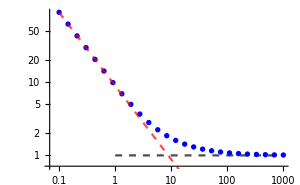

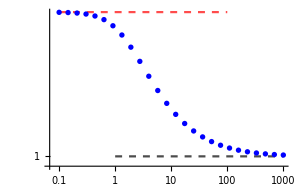

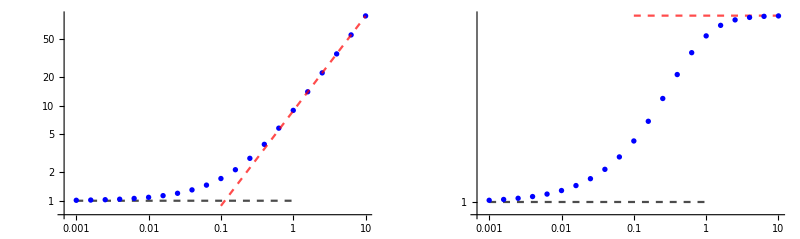

```mathematica
dataQ=Table[{Rvalues[[n]],Qvalues[[n]]/(8 π/15 Rvalues[[n]]^5)},{n,1,Length@Rvalues}]
ListLogLogPlot[dataQ,PlotRange->All,
AxesLabel->{MaTeX["R_s"],MaTeX[" \\frac{15}{8 \\pi V_b R_s^5} Q_s"]},
PlotStyle->Blue,ImageSize->300,PlotRange->All
];
LogLogPlot[1,{z,1,1000},PlotStyle->{Dashed,Black,Opacity[0.7]},ImageSize->300];
LogLogPlot[{-10000, (3/2 π^2 z^4)/(8 π/15 z^5)},{z,1/10,100},PlotStyle->{{Dashed,Black,Opacity[0.7]},{Dashed,Red,Opacity[0.7]}},ImageSize->300];
a2=Show[%%%,%%,%]
dataV=Table[{Rvalues[[n]],(Vvalues[[n]]+1)/Rvalues[[n]]^2},{n,1,Length@Rvalues}];
ListLogLogPlot[dataV,PlotRange->All,AxesLabel->{MaTeX["R_s"],MaTeX["\\frac{1}{V_b z_s R_s^2} \\tilde{V}_s"]},
PlotStyle->Blue,ImageSize->300];
LogLogPlot[ 1,{z,1,1000},PlotStyle->{Dashed,Black,Opacity[0.7]},ImageSize->300];
LogLogPlot[{-10000,3/2},{z,1/10,100},PlotStyle->{{Dashed,Black,Opacity[0.7]},{Dashed,Red,Opacity[0.7]}}, (*PlotLegends->{MaTeX["\\tilde{V}_s = V_b z_sR_s^2, \\quad Q_s = \\frac{8 \\pi}{15} V_b R_s^5 "],MaTeX["\\tilde{V}_s = \\frac{3}{2} V_b z_sR_s^2, \\quad Q_s = \\frac{3 \\pi^2}{2} V_b R_s^4 z_s "]}*)ImageSize->300];
b2=Show[%%%,%%,%]
GraphicsRow[{a,b}]
```

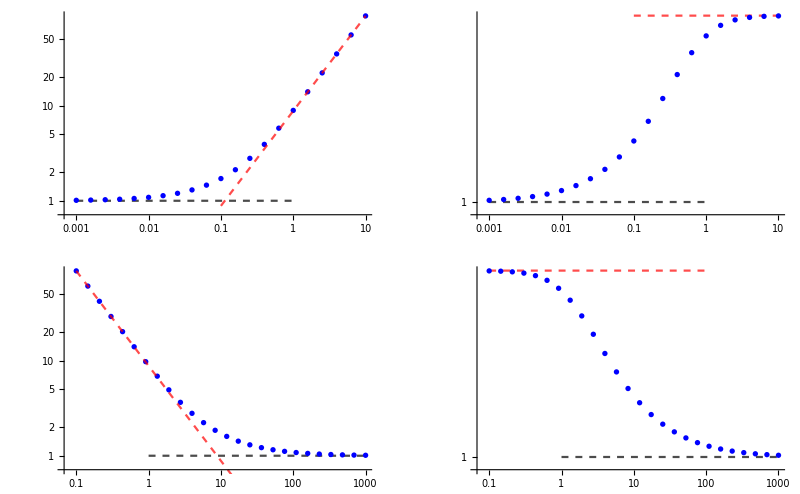

-Graphics-

```mathematica
GraphicsGrid[{{a,b},{a2,b2}}]
GraphicsGrid[{{a,b}}]
```

```mathematica
w = z-√(z^2-1);
Gp = -6 π^2 zs w^2;
D[%,z]//Simplify
%/.{z->r + I ϵ};
%%/.{z->r - I ϵ};
Assuming[0<r<1 && ϵ>0,Series[%%-%,{ϵ,0,0}]]
```

(12 π^2 (z-√(-1+z^2))^2 zs)/(√(-1+z^2))

-(24 ⅈ π^2 (-1+2 r^2) zs)/(√(1-r^2))+O[ϵ]^1

```mathematica
fpp=-(24 ⅈ π^2 (-1+2 r^2) zs)/(√(1-r^2)) I/(2π);
σ=-1/(2π r)Integrate[%,r]
```

6 √(1-r^2) zs

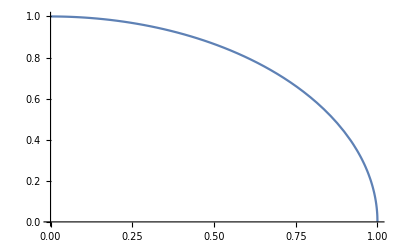

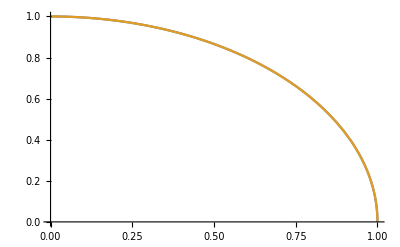

```mathematica
Plot[ √(1-r^2) ,{r,0,1}]
Plot[{Re[(150 (ⅈ-2 ⅈ r^2+(4 r)/(√(1-r^2))-(4 r^3)/(√(1-r^2))+(2 (-1+2 r^2) (Log[ⅈ r-√(1-r^2)]-Log[r+ⅈ √(1-r^2)]))/π))/(600 r)],√(1-r^2)},{r,0,1}]
```

```mathematica
<<MaTeX`
```

```mathematica
σlargez ={ ChargeDensity[4,1,1/1000],ChargeDensity[4,1,1/100],ChargeDensity[4,1,1/10],ChargeDensity[4,1,1],ChargeDensity[4,1,10],ChargeDensity[4,1,100]}
```

{{0.660825-0.496311 (-1+2 r)+0.014479 √(1-r^2)-0.164988 (1-6 r+6 r^2)+0.000380976 (-1+12 r-30 r^2+20 r^3)+0.0000939886 (1-20 r+90 r^2-140 r^3+70 r^4),0.00100381,8.06874×10^-16},{0.631814-0.477864 (-1+2 r)+0.100805 √(1-r^2)-0.156694 (1-6 r+6 r^2)+0.0022014 (-1+12 r-30 r^2+20 r^3)+0.000542742 (1-20 r+90 r^2-140 r^3+70 r^4),0.0102618,1.56682×10^-12},{0.428009-0.349694 (-1+2 r)+0.771537 √(1-r^2)-0.0981769 (1-6 r+6 r^2)+0.0158618 (-1+12 r-30 r^2+20 r^3)+0.00400073 (1-20 r+90 r^2-140 r^3+70 r^4),0.113889,1.30201×10^-9},{0.0130336-0.0124364 (-1+2 r)+6.06394 √(1-r^2)-0.00208447 (1-6 r+6 r^2)+0.00131597 (-1+12 r-30 r^2+20 r^3)+0.000171283 (1-20 r+90 r^2-140 r^3+70 r^4),0.435493,2.55218×10^-12},{0.00164285-0.000754081 (-1+2 r)+59.9978 √(1-r^2)-0.000362853 (1-6 r+6 r^2)-0.000349601 (-1+12 r-30 r^2+20 r^3)-0.000176313 (1-20 r+90 r^2-140 r^3+70 r^4),-985.009,0.},{0.0164501-0.00754753 (-1+2 r)+599.977 √(1-r^2)-0.00363304 (1-6 r+6 r^2)-0.00350292 (-1+12 r-30 r^2+20 r^3)-0.0017666 (1-20 r+90 r^2-140 r^3+70 r^4),-999850.,0.}}

```mathematica
σlargez ={{0.6608246058957239-0.4963111711484348 (-1+2 r)+0.01447898190430145 √(1-r^2)-0.1649883996150825 (1-6 r+6 r^2)+0.00038097631141177424 (-1+12 r-30 r^2+20 r^3)+0.00009398855654191095 (1-20 r+90 r^2-140 r^3+70 r^4),0.0010038073774825444,8.068742681920267*^-16},{0.6318143003056061-0.4778640817727818 (-1+2 r)+0.10080528364498784 √(1-r^2)-0.15669436189493655 (1-6 r+6 r^2)+0.002201401910651105 (-1+12 r-30 r^2+20 r^3)+0.0005427415438259375 (1-20 r+90 r^2-140 r^3+70 r^4),0.010261802342589619,1.566820810464456*^-12},{0.4280085376559596-0.3496941119177922 (-1+2 r)+0.7715373339030733 √(1-r^2)-0.09817690892421184 (1-6 r+6 r^2)+0.015861772625676868 (-1+12 r-30 r^2+20 r^3)+0.004000725753566136 (1-20 r+90 r^2-140 r^3+70 r^4),0.11388883229843225,1.3020072797687021*^-9},{0.013033604280772416-0.012436388532773814 (-1+2 r)+6.063938072813701 √(1-r^2)-0.0020844682625370706 (1-6 r+6 r^2)+0.0013159693853142939 (-1+12 r-30 r^2+20 r^3)+0.00017128324984413233 (1-20 r+90 r^2-140 r^3+70 r^4),0.4354931825467559,2.55218068900831*^-12},{0.0016428486779301575-0.0007540811373769796 (-1+2 r)+59.997795883241835 √(1-r^2)-0.00036285348332616983 (1-6 r+6 r^2)-0.00034960062914460023 (-1+12 r-30 r^2+20 r^3)-0.00017631255069903314 (1-20 r+90 r^2-140 r^3+70 r^4),-985.0093528844016,0.},{0.016450098544050978-0.007547532448242224 (-1+2 r)+599.9765301086928 √(1-r^2)-0.003633038406858832 (1-6 r+6 r^2)-0.003502922808284665 (-1+12 r-30 r^2+20 r^3)-0.0017665964527168545 (1-20 r+90 r^2-140 r^3+70 r^4),-999850.0011828508,0.}};
```

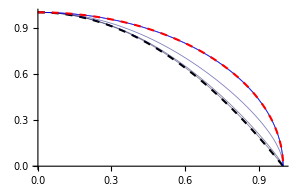

-Graphics-

-Graphics-

```mathematica
{1-r^2}~Join~Table[(σlargez[[i]][[1]])/(σlargez[[i]][[1]]/.{r->0}),{i,1,6}]~Join~{√(1-r^2)};
Plot[%,{r,0,1},
AxesLabel->{MaTeX["\\frac{r}{R_s}"],MaTeX["\\frac{\\sigma(r)}{\\sigma(0)}"]},
PlotLegends->{MaTeX["1-r^2 "],MaTeX["z_{s}=10^{-3}"],MaTeX["z_{s}=10^{-2}"],MaTeX["z_{s}=10^{-1}"],MaTeX["z_{s}=1"],MaTeX["z_{s}=10"],MaTeX["z_{s}=10^2"],MaTeX["\\sqrt{1-r^2}"]},
PlotStyle->{{Black,Dashed,Thickness[0.005]},{RGBColor[0,0,2/12,0.5],Thickness[0.002]},{RGBColor[0,0,4/12,0.5],Thickness[0.002]},{RGBColor[0,0,6/12,0.5],Thickness[0.002]},{RGBColor[0,0,8/12,0.5],Thickness[0.002]},{RGBColor[0,0,10/12,0.5],Thickness[0.002]},{RGBColor[0,0,12/12,0.5],Thickness[0.002]},{Red,Dashed,Thickness[0.005]}},
ImageSize->300,PlotRangePadding->0,PlotRange->All
]
GraphicsRow[{%},ImageSize->Full,Spacings->{0,0},PlotRangePadding->0,Spacings->{2,2}]
(*Plot[Re[(150 (ⅈ-2 ⅈ r^2+(4 r)/(√(1-r^2))-(4 r^3)/(√(1-r^2))+(2 (-1+2 r^2) (Log[ⅈ r-√(1-r^2)]-Log[r+ⅈ √(1-r^2)]))/π))/(600 r)],{r,0,1},
AxesLabel->{MaTeX["r"],MaTeX["\\frac{\\sigma(r)}{\\sigma(0)}"]},
PlotStyle->{Black,Dashed,Thick},
ImageSize->300,PlotRangePadding->0,PlotRange->All
]

Plot[(1-r^2) ,{r,0,1},
AxesLabel->{MaTeX["r"],MaTeX["\\frac{\\sigma(r)}{\\sigma(0)}"]},
PlotStyle->{Black,Dashed},
ImageSize->300,PlotRangePadding->0,PlotRange->All
]
Show[%%,%,%%%]*)
```

```mathematica
(* Convergence *)
σ= Table[ ChargeDensity[2n,10,1],{n,1,5}];
```

```mathematica
σlargez
```

{{0.00164285-0.000754081 (-1+2 r)+59.9978 √(1-r^2)-0.000362853 (1-6 r+6 r^2)-0.000349601 (-1+12 r-30 r^2+20 r^3)-0.000176313 (1-20 r+90 r^2-140 r^3+70 r^4),-985.009,0.},{0.0164501-0.00754753 (-1+2 r)+599.977 √(1-r^2)-0.00363304 (1-6 r+6 r^2)-0.00350292 (-1+12 r-30 r^2+20 r^3)-0.0017666 (1-20 r+90 r^2-140 r^3+70 r^4),-999850.,0.},{0.218198-0.103316 (-1+2 r)+5999.69 √(1-r^2)-0.0506349 (1-6 r+6 r^2)-0.0431905 (-1+12 r-30 r^2+20 r^3)-0.0210555 (1-20 r+90 r^2-140 r^3+70 r^4),-9.99999×10^8,0.},{55.4704-28.8185 (-1+2 r)+59926.6 √(1-r^2)-14.8021 (1-6 r+6 r^2)-8.37973 (-1+12 r-30 r^2+20 r^3)-3.46905 (1-20 r+90 r^2-140 r^3+70 r^4),-1.×10^12,0.},{-91728.1+47629.9 (-1+2 r)+720782. √(1-r^2)+24197.5 (1-6 r+6 r^2)+13996.9 (-1+12 r-30 r^2+20 r^3)+5901.88 (1-20 r+90 r^2-140 r^3+70 r^4),-1.×10^15,0.}}

```mathematica
σ = {{55.06598902686811-41.33856907298013 (-1+r/5)+6.030408583517171 √(100-r^2)-0.27451082922611386 (50-30 r+3 r^2),113.20852545409659,0.022382313734851778},{42.799285741490664-34.96877295900019 (-1+r/5)+7.715594318486321 √(100-r^2)-0.19633759701393383 (50-30 r+3 r^2)+0.03172051050119252 (-50+60 r-15 r^2+r^3)+0.0004004933555282526 (1000-2000 r+900 r^2-140 r^3+7 r^4),113.8889231788975,0.0013013322313781828},{35.91116950114734-31.643364984267514 (-1+r/5)+8.627211918912726 √(100-r^2)-0.15951079171194113 (50-30 r+3 r^2)+0.04613220584532261 (-50+60 r-15 r^2+r^3)+0.0009500428685906093 (1000-2000 r+900 r^2-140 r^3+7 r^4)+0.000014277932600788684 (-25000+75000 r-52500 r^2+14000 r^3-1575 r^4+63 r^5)+3.7656543307178757*^-7 (250000-1050000 r+1050000 r^2-420000 r^3+78750 r^4-6930 r^5+231 r^6),114.09293923647327,0.000032765965443104506},{33.5623519818666-30.53711373106147 (-1+r/5)+8.933590638546551 √(100-r^2)-0.14767648412984538 (50-30 r+3 r^2)+0.050581130703298616 (-50+60 r-15 r^2+r^3)+0.0011114405023475982 (1000-2000 r+900 r^2-140 r^3+7 r^4)+0.00001845862292058771 (-25000+75000 r-52500 r^2+14000 r^3-1575 r^4+63 r^5)+7.218328473220809*^-7 (250000-1050000 r+1050000 r^2-420000 r^3+78750 r^4-6930 r^5+231 r^6)+4.9191140898176914*^-8 (-1250000+7000000 r-9450000 r^2+5250000 r^3-1443750 r^4+207900 r^5-15015 r^6+429 r^7)+1.467640368852327*^-9 (10000000-72000000 r+126000000 r^2-92400000 r^3+34650000 r^4-7207200 r^5+840840 r^6-51480 r^7+1287 r^8),114.13685374658745,1.7843558453023434*^-7},{33.27685009162196-30.404329152359182 (-1+r/5)+8.970574948282463 √(100-r^2)-0.1462692327979711 (50-30 r+3 r^2)+0.05109110795671942 (-50+60 r-15 r^2+r^3)+0.0011295767357696858 (1000-2000 r+900 r^2-140 r^3+7 r^4)+0.000018903365989026434 (-25000+75000 r-52500 r^2+14000 r^3-1575 r^4+63 r^5)+7.635403276930234*^-7 (250000-1050000 r+1050000 r^2-420000 r^3+78750 r^4-6930 r^5+231 r^6)+5.4527704117764*^-8 (-1250000+7000000 r-9450000 r^2+5250000 r^3-1443750 r^4+207900 r^5-15015 r^6+429 r^7)+2.0441260056105097*^-9 (10000000-72000000 r+126000000 r^2-92400000 r^3+34650000 r^4-7207200 r^5+840840 r^6-51480 r^7+1287 r^8)+8.80467182544601*^-11 (-50000000+450000000 r-990000000 r^2+924000000 r^3-450450000 r^4+126126000 r^5-21021000 r^6+2059200 r^7-109395 r^8+2431 r^9)+1.34440090689409*^-13 (2500000000-27500000000 r+74250000000 r^2-85800000000 r^3+52552500000 r^4-18918900000 r^5+4204200000 r^6-583440000 r^7+49227750 r^8-2309450 r^9+46189 r^10),114.14064543503014,3.39787220582366*^-9}};
```

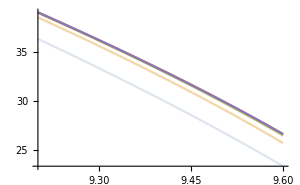

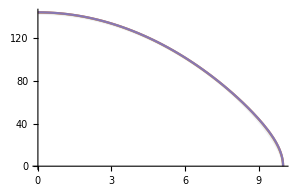

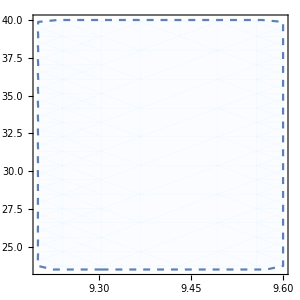

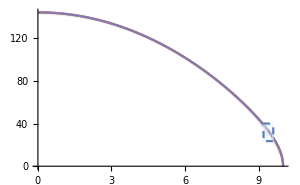

```mathematica
Table[σ[[i]][[1]],{i,1,5}];
p1=Plot[%,{r,9.2,9.6},PlotStyle->{{Opacity[0.2]},{Opacity[0.4]},{Opacity[0.6]},{Opacity[0.8]},{Opacity[1]}},
AxesLabel->{MaTeX["r"],MaTeX["\\sigma(r)"]},
PlotLegends->{MaTeX["N_{max}=2"],MaTeX["N_{max}=4"],MaTeX["N_{max}=6"],MaTeX["N_{max}=8"],MaTeX["N_{max}=10"]},
ImageSize->300,PlotRangePadding->0,PlotRange->All
]
Table[σ[[i]][[1]],{i,1,5}];
p2=Plot[%,{r,0,10},PlotStyle->{{Opacity[0.1]},{Opacity[0.3]},{Opacity[0.5]},{Opacity[0.7]},{Opacity[1]}},
AxesLabel->{MaTeX["r"],MaTeX["\\sigma(r)"]},
ImageSize->300,PlotRangePadding->0,PlotRange->All
]
RegionPlot[9.2<r<9.6 && 23.5<y<40,{r,0,10},{y,0,150},BoundaryStyle->Dashed,PlotStyle->{LightBlue,Opacity[0.15]},
ImageSize->300,PlotRangePadding->0,PlotRange->All,PlotPoints->80
]
GraphicsRow[{Show[p2,%],Show[p1,%]},ImageSize->Full,Spacings->{0,0},PlotRangePadding->0,Spacings->{2,2},PlotRange->All];
Show[%,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["convergence.pdf"]]]
```

```mathematica
Export["/Users/antoinevuignier/Desktop/convergence.pdf",%280,"PDF"]
```

/Users/antoinevuignier/Desktop/convergence.pdf

```mathematica
Export["/Users/antoinevuignier/Desktop/convergence_pdf.pdf",%273,"PDF"]
```

/Users/antoinevuignier/Desktop/convergence_pdf.pdf

```mathematica
σ= Table[ ChargeDensity[3,10,10^-n],{n,1,4}]
```

```mathematica
σ={{32.24193722899338+5.1930117415431765 √(100-r^2)+26.434369055213065 Cos[(π r)/10]-4.47030438147837 Cos[(π r)/5]+1.3373134376652132 Cos[(3 π r)/10],10.421914020134386,0.001561841110401474},{33.60094205811475+4.443086845645475 √(100-r^2)+27.464048099572125 Cos[(π r)/10]-4.724811420565062 Cos[(π r)/5]+1.4120830922049845 Cos[(3 π r)/10],1.0128061278541058,0.000022120754370247298},{34.151038885784025+4.245611026142198 √(100-r^2)+27.86923877570403 Cos[(π r)/10]-4.8313194762538565 Cos[(π r)/5]+1.4504806393956524 Cos[(3 π r)/10],0.10040624650241545,2.4058340155480584*^-7},{34.34256507560652+4.186152960486704 √(100-r^2)+28.00896855277575 Cos[(π r)/10]-4.8688451717071075 Cos[(π r)/5]+1.4647513511793102 Cos[(3 π r)/10],0.010013542800910089,2.466239660409153*^-9}};
```

{100-r^2,32.2419+5.19301 √(100-r^2)+26.4344 Cos[(π r)/10]-4.4703 Cos[(π r)/5]+1.33731 Cos[(3 π r)/10],33.6009+4.44309 √(100-r^2)+27.464 Cos[(π r)/10]-4.72481 Cos[(π r)/5]+1.41208 Cos[(3 π r)/10],34.151+4.24561 √(100-r^2)+27.8692 Cos[(π r)/10]-4.83132 Cos[(π r)/5]+1.45048 Cos[(3 π r)/10],34.3426+4.18615 √(100-r^2)+28.009 Cos[(π r)/10]-4.86885 Cos[(π r)/5]+1.46475 Cos[(3 π r)/10]}

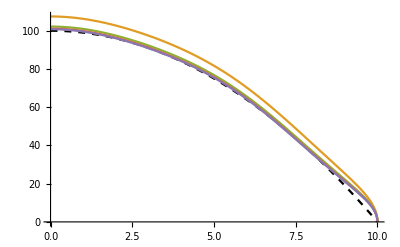

```mathematica
{100-r^2}~Join~Table[σ[[i]][[1]],{i,1,4}]
Plot[%,{r,0,10},PlotStyle->{{Black,Dashed},Plain,Plain,Plain,Plain}]
```

```mathematica
Quit[]
```

```mathematica
ClearAll[a,V0,α,q,d]
a=(√(2/3) √(V0+d^3 α))/(√d √α);
V0=(√(3/2) √d √q √α)/π-d^3 α;
(*α=2;*)
q=(3 d π^2)/2;
d=100;
rσ=-3 ⅈ d r^2 α-(6 d r^3 α)/(√((a-r) (a+r)))+ⅈ (V0+d^3 α)+(r (2 V0+3 a^2 d α+2 d^3 α))/(√((a-r) (a+r)))+(2 (V0+d (d^2-3 r^2) α) (-Log[ⅈ r-√(a^2-r^2)]+Log[r+ⅈ √(a^2-r^2)]))/π;
Assuming[1>r>0 && α>0,%/r//Simplify]
Plot[Re[(%%)/r]-6 d √α √(1/(√α)-r^2),{r,0,a},PlotPoints->10]
4π NIntegrate[r^2 Re[(%%)/r],{r,0,a}]
a//N
ClearAll[a,V0,α,q,d]
```

(150 ((4 r)/(√(1/α^(3/2)-r^2/α))+ⅈ √α-2 ⅈ r^2 α-(4 r^3 α)/(√(-r^2+1/(√α)))+(2 (-√α+2 r^2 α) (Log[ⅈ r-√(-r^2+1/(√α))]-Log[r+ⅈ √(-r^2+1/(√α))]))/π))/r

Plot::plln: Limiting value 1/α^(1/4) in {r,0,1/α^(1/4)} is not a machine-sized real number.

Plot[Re[(%%)/r]-6 d √α √(1/(√α)-r^2),{r,0,a},PlotPoints→10]

NIntegrate::nlim: r = 1/α^(1/4) is not a valid limit of integration.

4 π NIntegrate[r^2 Re[(%%)/r],{r,0,a}]

1/α^(1/4)

```mathematica
V0=(√(3/2) √d √q √α)/π-d^3 α;
α=1;
a=(√(2/3) √(V0+d^3 α))/(√d √α)//PowerExpand
Solve[%==1,q]

ClearAll[a,V0,α,q,d]
```

((2/3)^(1/4) q^(1/4))/(d^(1/4) √π)

{{q→(3 d π^2)/2}}

{{c[0]→2 (c[1]-c[2]+c[3])}}

{0.,{c[1]→0.00486386,c[2]→-0.00183812,c[3]→0.00199393,c[4]→5999.86,V0→-1.×10^9}}

3.11566×10^-10

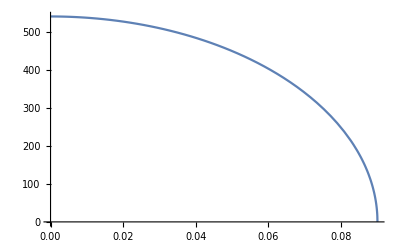

0.97131

```mathematica
ClearAll[Vb,d,Rs,nn,ngrid,vars,σ,V,Vbg,EOM,constr,sol,Q]
(* parameters *)
Vb=1;
d=1000;
Rs=0.09(*065718901896307*);
nn=3;
ngrid = 20;
vars = Table[c[n],{n,1,nn+1}]~Join~{V0};

(* --------------------------- *)

(* charge density σ = c[0]/2+Sum[c[n]Cos[ π n r/Rs],{n,1,nn}]+ c[nn+1] √(Rs^2-r^2); *)
σ[r_]:= {1/2}~Join~Table[ Cos[ (π n r)/Rs],{n,1,nn}]~Join~{√(Rs^2-r^2)};

(* it vanishes at the edge *)
sol1=Solve[c[0]/2+Sum[c[n]Cos[ π n],{n,1,nn}]==0,c[0]]
(* Potential at z=d where the disk is *)
V[r_?NumericQ]:=1/(4π r)NIntegrate[u σ[u] Log[(1+(4 r u)/(r-u)^2)/(1+(4 r u)/((r-u)^2+4 d^2))],{u,0,r,Rs},Method->"PrincipalValue"];
(* background potential *)
Vbg[r_]:= Vb(r^2 d-d^3);


(* equations of motion V_disk + V_bg = V0 *)
EOM[r_?NumericQ]:= (Sum[ c[n] V[r][[n+1]],{n,0,nn+1}]+Vbg[r]-V0)/.sol1[[1]];

(* constraints : EOM =0 at r= r_i and σ(r=Rs)=0 *)
sol1=Solve[c[0]/2+Sum[c[n]Cos[ π n],{n,1,nn}]==0,c[0]];
constr = Sum[ EOM[n Rs/ngrid]^2,{n,1,ngrid}](*+(c[0]/2+Sum[c[n]Cos[ π n],{n,1,nn}])^2*);
sol=NMinimize[constr,vars,PrecisionGoal->6]


constr/.sol[[2]]

(* charge density *)
c[0]/2+Sum[c[n]Cos[ π n r/Rs],{n,1,nn}]+c[nn+1](√(Rs^2-r^2))/.sol1[[1]]/.sol[[2]];
Plot[%,{r,0,Rs}]

(* total charge *)
Q = 4π NIntegrate[r^2%%,{r,0,Rs}]

ClearAll[Vb,d,Rs,nn,ngrid,vars,σ,V,Vbg,EOM,constr,sol,Q]
```

{0.000483101,{c[0]→85.2303,c[1]→30.9094,c[2]→-6.56261,c[3]→2.50465,c[4]→-1.22585,c[5]→0.656983,c[6]→-0.393396,c[7]→0.220952,c[8]→-0.141334,c[9]→3.72839,V0→10.3365}}

0.000483101

9999/1000

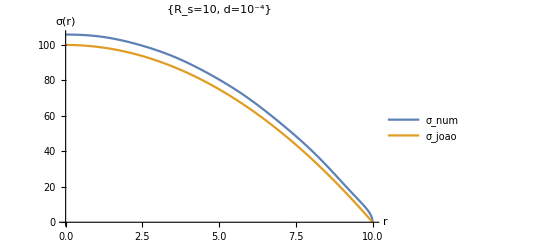

186597.

167552.

```mathematica
ClearAll[Vb,d,Rs,nn,ngrid,vars,σ,V,Vbg,EOM,constr,sol,Q]
(* parameters *)
Vb=1;
d=1/10;
Rs=10;
nn=8;
ngrid = 2nn;
vars = Table[c[n],{n,0,nn+1}]~Join~{V0};

(* --------------------------- *)

(* charge density σ = c[0]/2+Sum[c[n]Cos[ π n r/Rs],{n,1,nn}]+ c[nn+1] √(Rs^2-r^2); *)
σ[r_]:= {1/2}~Join~Table[ Cos[ (π n r)/Rs],{n,1,nn}]~Join~{√(Rs^2-r^2)};
(* Potential at z=d where the disk is *)
V[r_?NumericQ]:=1/(4π r)NIntegrate[u σ[u] Log[(1+(4 r u)/(r-u)^2)/(1+(4 r u)/((r-u)^2+4 d^2))],{u,0,r,Rs},Method->"PrincipalValue",WorkingPrecision->10,AccuracyGoal->10];
(* background potential *)
Vbg[r_]:= Vb(r^2 d-d^3);


(* equations of motion V_disk + V_bg = V0 *)
EOM[r_?NumericQ]:= Sum[ c[n] V[r][[n+1]],{n,0,nn+1}]+Vbg[r]-V0;

(* constraints : EOM =0 at r= r_i and σ(r=Rs)=0 *)
constr = Sum[ EOM[n Rs/ngrid]^2,{n,1,ngrid}]+(c[0]/2+Sum[c[n]Cos[ π n],{n,1,nn}])^2;
sol=NMinimize[constr,vars,PrecisionGoal->10,AccuracyGoal->10]


constr/.sol[[2]]

σj = (Rs^2-r^2) Vb;
V0j=-Vb d^3+Vb d Rs^2

(* charge density *)
c[0]/2+Sum[c[n]Cos[ π n r/Rs],{n,1,nn}]+c[nn+1](√(Rs^2-r^2))/.sol[[2]];
Plot[{%,σj},{r,0,Rs},AxesLabel->{"r","σ(r)"},PlotLegends->{"σ_num","σ_joao"},PlotStyle->{"Plain","Dashed"},PlotLabel->{"R_s=10, d=10^-4"}]

(* total charge *)
Q = 4π NIntegrate[r^2%%,{r,0,Rs},PrecisionGoal->6]
8 π/15 Vb Rs^5//N

(* joao's prediction *)


(*Rs/(Q d)^(1/6)*)

ClearAll[Vb,d,Rs,nn,ngrid,vars,σ,V,Vbg,EOM,constr,sol,Q]
```

```mathematica
9999999999/1000000000000//N[#,6]&
```

0.01

```mathematica
sol={1.231991921782534*^-9,{c[0]->91.93557001175431,c[1]->32.858702113948034,c[2]->-7.213053017126882,c[3]->2.823517996341407,c[4]->-1.4075167509406936,c[5]->0.7679158815929051,c[6]->-0.46333379846231987,c[7]->0.2650590855796917,c[8]->-0.16868636195805078,c[9]->2.65408479685546,V0->0.01000938226637566}};
nn=8;
Rs=10;
c[0]/2+Sum[c[n]Cos[ π n r/Rs],{n,1,nn}]+c[nn+1](√(Rs^2-r^2))/.sol[[2]];
Plot[{%,σj},{r,0,10},AxesLabel->{"r","σ(r)"},PlotStyle->{Plain,Dashed},PlotLegends->{"σ_num","σ_joao"},PlotLabel->{"R_s=10, z_s=10^-4"}]
```

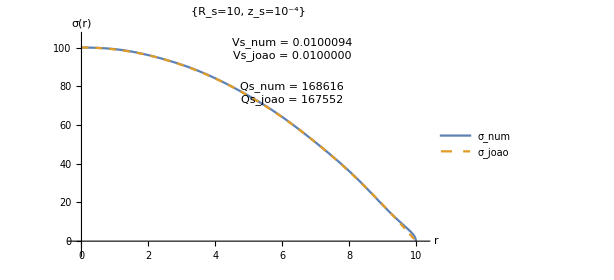

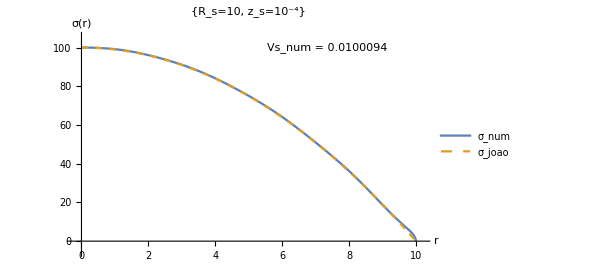

{{10,12.4105},{20,23.743},{30,34.9926},{40,46.2099},{50,57.4096}}

{{10.7971,12.4105},{20.6564,23.743},{30.4436,34.9926},{40.2026,46.2099},{49.9464,57.4096}}

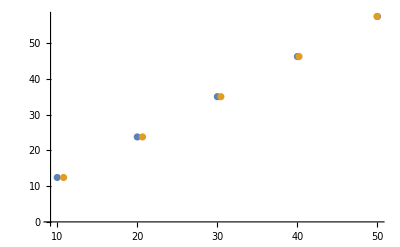

```mathematica
Rs={10,20,30,40,50};
NN={294401.2256864436,7.545350800876632*^6,5.24664061775869*^7,2.107050914392922*^8,6.236244734131043*^8};
Table[{Rs[[n]],NN[[n]]^(1/5)},{n,1,5}]
Table[{0.87 NN[[n]]^(1/5),NN[[n]]^(1/5)},{n,1,5}]
ListPlot[{%%,%}]

ClearAll[Rs,NN]
```

```mathematica
(* joao's prediction *)
σj = (Rs^2-r^2) Vb
V0j=-Vb d^3+Vb d Rs^2
```

(-r^2+Rs^2) Vb

```mathematica
ClearAll[k,ka]
k[J_,x_]:=Log[(Gamma[2/3+J-(8 ⅈ x)/3]^3 Gamma[2/3+J+(8 ⅈ x)/3]^3)/((J^2+(64 x^2)/9) Gamma[1/3+J-(8 ⅈ x)/3]^3 Gamma[1/3+J+(8 ⅈ x)/3]^3)]
ka[J_,x_]:=1/3(1/(3J+8I x)^2+ 1/(3J-8I x)^2)
```

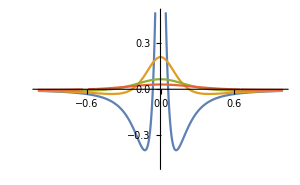

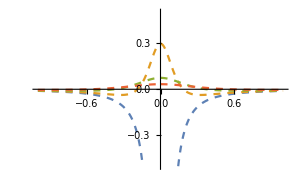

-Graphics-

```mathematica
Plot[{k[0,x],k[1/2,x],k[1,x],k[3/2,x]},{x,-1,1},PlotRange->{-1/2,1/2},
AxesLabel->{MaTeX["x"],MaTeX["k_{st}(x)"]},
PlotLegends->{MaTeX["J=0"],MaTeX["J=\\frac{1}{2}"],MaTeX["J=1"],MaTeX["J=\\frac{3}{2}"]},
ImageSize->300
]
Plot[{ka[0,x],ka[1/2,x],ka[1,x],ka[3/2,x]},{x,-1,1},PlotRange->{-1/2,1/2},PlotStyle->Dashed,ImageSize->300]
GraphicsRow[{Show[%%,%]}]
```

```mathematica
Table[Assuming[Ω>0,Ω^(2k)/( (2^16 π^(29/2))/3 ((128 √(3 π) (4294967296+81 Ω^4 (-20480+3 Ω^4))+9 ⅇ^((3 Ω^4)/16384) π Ω^2 ((1635778560+331776 Ω^4-81 Ω^8) Erfc[(√3 Ω^2)/128]-1048576000 ⅇ^((3 Ω^4)/2048) Erfc[(3 √3 Ω^2)/128]))/(12884901888 Ω^2))+5^3 2^8 π^(31/2)ⅇ^(27/2^14 Ω^4))( (2^17 π^(29/2))/3(-1/2^8)^k Integrate[ ((4+x^2)^3 x^2)/((1+x^2)^3(9+x^2))x^(2k)ⅇ^(-3 Ω^4/2^14 x^2),{x,-Infinity,Infinity}]+5^3 2^9 π^(31/2)(3/16)^(2k)ⅇ^(27/2^14 Ω^4))],{k,1,3}]
```

{(Ω^2 (2250 ⅇ^((27 Ω^4)/16384) π^(31/2)-(π^(29/2) (-128 √(3 π) (-35184372088832+729 Ω^8 (4096+Ω^4))+81 ⅇ^((3 Ω^4)/16384) π Ω^6 ((-1149239296+184320 Ω^4+27 Ω^8) Erfc[(√3 Ω^2)/128]+3145728000 ⅇ^((3 Ω^4)/2048) Erfc[(3 √3 Ω^2)/128])))/(226492416 Ω^6)))/(32000 ⅇ^((27 Ω^4)/16384) π^(31/2)+(π^(29/2) (128 √(3 π) (4294967296+81 Ω^4 (-20480+3 Ω^4))+9 ⅇ^((3 Ω^4)/16384) π Ω^2 ((1635778560+331776 Ω^4-81 Ω^8) Erfc[(√3 Ω^2)/128]-1048576000 ⅇ^((3 Ω^4)/2048) Erfc[(3 √3 Ω^2)/128])))/(589824 Ω^2)),(Ω^4 (10125/128 ⅇ^((27 Ω^4)/16384) π^(31/2)+(π^(29/2) (128 √(3 π) (288230376151711744+27 Ω^8 (8589934592+405504 Ω^4+27 Ω^8))+81 ⅇ^((3 Ω^4)/16384) π Ω^10 ((142606336-9 Ω^4 (53248+3 Ω^4)) Erfc[(√3 Ω^2)/128]-28311552000 ⅇ^((3 Ω^4)/2048) Erfc[(3 √3 Ω^2)/128])))/(57982058496 Ω^10)))/(32000 ⅇ^((27 Ω^4)/16384) π^(31/2)+(π^(29/2) (128 √(3 π) (4294967296+81 Ω^4 (-20480+3 Ω^4))+9 ⅇ^((3 Ω^4)/16384) π Ω^2 ((1635778560+331776 Ω^4-81 Ω^8) Erfc[(√3 Ω^2)/128]-1048576000 ⅇ^((3 Ω^4)/2048) Erfc[(3 √3 Ω^2)/128])))/(589824 Ω^2)),(Ω^6 ((91125 ⅇ^((27 Ω^4)/16384) π^(31/2))/32768-(π^(29/2) (-128 √(3 π) (-11805916207174113034240+27 Ω^8 (-70368744177664+3 Ω^4 (85899345920+700416 Ω^4+27 Ω^8)))+243 ⅇ^((3 Ω^4)/16384) π Ω^14 ((2474639360+27 Ω^4 (28672+Ω^4)) Erfc[(√3 Ω^2)/128]+254803968000 ⅇ^((3 Ω^4)/2048) Erfc[(3 √3 Ω^2)/128])))/(44530220924928 Ω^14)))/(32000 ⅇ^((27 Ω^4)/16384) π^(31/2)+(π^(29/2) (128 √(3 π) (4294967296+81 Ω^4 (-20480+3 Ω^4))+9 ⅇ^((3 Ω^4)/16384) π Ω^2 ((1635778560+331776 Ω^4-81 Ω^8) Erfc[(√3 Ω^2)/128]-1048576000 ⅇ^((3 Ω^4)/2048) Erfc[(3 √3 Ω^2)/128])))/(589824 Ω^2))}

```mathematica
{(Ω^2 (2250 ⅇ^((27 Ω^4)/16384) π^(31/2)-(π^(29/2) (-128 √(3 π) (-35184372088832+729 Ω^8 (4096+Ω^4))+81 ⅇ^((3 Ω^4)/16384) π Ω^6 ((-1149239296+184320 Ω^4+27 Ω^8) Erfc[(√3 Ω^2)/128]+3145728000 ⅇ^((3 Ω^4)/2048) Erfc[(3 √3 Ω^2)/128])))/(226492416 Ω^6)))/(32000 ⅇ^((27 Ω^4)/16384) π^(31/2)+(π^(29/2) (128 √(3 π) (4294967296+81 Ω^4 (-20480+3 Ω^4))+9 ⅇ^((3 Ω^4)/16384) π Ω^2 ((1635778560+331776 Ω^4-81 Ω^8) Erfc[(√3 Ω^2)/128]-1048576000 ⅇ^((3 Ω^4)/2048) Erfc[(3 √3 Ω^2)/128])))/(589824 Ω^2)),(Ω^4 (10125/128 ⅇ^((27 Ω^4)/16384) π^(31/2)+(π^(29/2) (128 √(3 π) (288230376151711744+27 Ω^8 (8589934592+405504 Ω^4+27 Ω^8))+81 ⅇ^((3 Ω^4)/16384) π Ω^10 ((142606336-9 Ω^4 (53248+3 Ω^4)) Erfc[(√3 Ω^2)/128]-28311552000 ⅇ^((3 Ω^4)/2048) Erfc[(3 √3 Ω^2)/128])))/(57982058496 Ω^10)))/(32000 ⅇ^((27 Ω^4)/16384) π^(31/2)+(π^(29/2) (128 √(3 π) (4294967296+81 Ω^4 (-20480+3 Ω^4))+9 ⅇ^((3 Ω^4)/16384) π Ω^2 ((1635778560+331776 Ω^4-81 Ω^8) Erfc[(√3 Ω^2)/128]-1048576000 ⅇ^((3 Ω^4)/2048) Erfc[(3 √3 Ω^2)/128])))/(589824 Ω^2)),(Ω^6 ((91125 ⅇ^((27 Ω^4)/16384) π^(31/2))/32768-(π^(29/2) (-128 √(3 π) (-11805916207174113034240+27 Ω^8 (-70368744177664+3 Ω^4 (85899345920+700416 Ω^4+27 Ω^8)))+243 ⅇ^((3 Ω^4)/16384) π Ω^14 ((2474639360+27 Ω^4 (28672+Ω^4)) Erfc[(√3 Ω^2)/128]+254803968000 ⅇ^((3 Ω^4)/2048) Erfc[(3 √3 Ω^2)/128])))/(44530220924928 Ω^14)))/(32000 ⅇ^((27 Ω^4)/16384) π^(31/2)+(π^(29/2) (128 √(3 π) (4294967296+81 Ω^4 (-20480+3 Ω^4))+9 ⅇ^((3 Ω^4)/16384) π Ω^2 ((1635778560+331776 Ω^4-81 Ω^8) Erfc[(√3 Ω^2)/128]-1048576000 ⅇ^((3 Ω^4)/2048) Erfc[(3 √3 Ω^2)/128])))/(589824 Ω^2))};
Assuming[Ω>0, %//FullSimplify]
```

{(-128 √3 (-35184372088832+729 Ω^8 (4096+Ω^4))+81 ⅇ^((3 Ω^4)/16384) √π Ω^6 (-1149239296+184320 Ω^4+27 Ω^8) Erfc[(√3 Ω^2)/128]+254803968000 ⅇ^((27 Ω^4)/16384) √π Ω^6 (-2+Erfc[(3 √3 Ω^2)/128]))/(384 Ω^2 (-128 √3 (4294967296+81 Ω^4 (-20480+3 Ω^4))+27 ⅇ^((3 Ω^4)/16384) √π Ω^2 (-545259520+27 Ω^4 (-4096+Ω^4)) Erfc[(√3 Ω^2)/128]+9437184000 ⅇ^((27 Ω^4)/16384) √π Ω^2 (-2+Erfc[(3 √3 Ω^2)/128]))),(-128 √3 (288230376151711744+27 Ω^8 (8589934592+405504 Ω^4+27 Ω^8))+81 ⅇ^((3 Ω^4)/16384) √π Ω^10 (-142606336+479232 Ω^4+27 Ω^8) Erfc[(√3 Ω^2)/128]+2293235712000 ⅇ^((27 Ω^4)/16384) √π Ω^10 (-2+Erfc[(3 √3 Ω^2)/128]))/(98304 Ω^4 (-128 √3 (4294967296+81 Ω^4 (-20480+3 Ω^4))+27 ⅇ^((3 Ω^4)/16384) √π Ω^2 (-545259520+27 Ω^4 (-4096+Ω^4)) Erfc[(√3 Ω^2)/128]+9437184000 ⅇ^((27 Ω^4)/16384) √π Ω^2 (-2+Erfc[(3 √3 Ω^2)/128]))),(-128 √3 (-11805916207174113034240+27 Ω^8 (-70368744177664+3 Ω^4 (85899345920+700416 Ω^4+27 Ω^8)))+243 ⅇ^((3 Ω^4)/16384) √π Ω^14 (2474639360+27 Ω^4 (28672+Ω^4)) Erfc[(√3 Ω^2)/128]+61917364224000 ⅇ^((27 Ω^4)/16384) √π Ω^14 (-2+Erfc[(3 √3 Ω^2)/128]))/(75497472 Ω^6 (-128 √3 (4294967296+81 Ω^4 (-20480+3 Ω^4))+27 ⅇ^((3 Ω^4)/16384) √π Ω^2 (-545259520+27 Ω^4 (-4096+Ω^4)) Erfc[(√3 Ω^2)/128]+9437184000 ⅇ^((27 Ω^4)/16384) √π Ω^2 (-2+Erfc[(3 √3 Ω^2)/128])))}

```mathematica
ϕ= {(-128 √3 (-35184372088832+729 Ω^8 (4096+Ω^4))+81 ⅇ^((3 Ω^4)/16384) √π Ω^6 (-1149239296+184320 Ω^4+27 Ω^8) Erfc[(√3 Ω^2)/128]+254803968000 ⅇ^((27 Ω^4)/16384) √π Ω^6 (-2+Erfc[(3 √3 Ω^2)/128]))/(384 Ω^2 (-128 √3 (4294967296+81 Ω^4 (-20480+3 Ω^4))+27 ⅇ^((3 Ω^4)/16384) √π Ω^2 (-545259520+27 Ω^4 (-4096+Ω^4)) Erfc[(√3 Ω^2)/128]+9437184000 ⅇ^((27 Ω^4)/16384) √π Ω^2 (-2+Erfc[(3 √3 Ω^2)/128]))),(-128 √3 (288230376151711744+27 Ω^8 (8589934592+405504 Ω^4+27 Ω^8))+81 ⅇ^((3 Ω^4)/16384) √π Ω^10 (-142606336+479232 Ω^4+27 Ω^8) Erfc[(√3 Ω^2)/128]+2293235712000 ⅇ^((27 Ω^4)/16384) √π Ω^10 (-2+Erfc[(3 √3 Ω^2)/128]))/(98304 Ω^4 (-128 √3 (4294967296+81 Ω^4 (-20480+3 Ω^4))+27 ⅇ^((3 Ω^4)/16384) √π Ω^2 (-545259520+27 Ω^4 (-4096+Ω^4)) Erfc[(√3 Ω^2)/128]+9437184000 ⅇ^((27 Ω^4)/16384) √π Ω^2 (-2+Erfc[(3 √3 Ω^2)/128]))),(-128 √3 (-11805916207174113034240+27 Ω^8 (-70368744177664+3 Ω^4 (85899345920+700416 Ω^4+27 Ω^8)))+243 ⅇ^((3 Ω^4)/16384) √π Ω^14 (2474639360+27 Ω^4 (28672+Ω^4)) Erfc[(√3 Ω^2)/128]+61917364224000 ⅇ^((27 Ω^4)/16384) √π Ω^14 (-2+Erfc[(3 √3 Ω^2)/128]))/(75497472 Ω^6 (-128 √3 (4294967296+81 Ω^4 (-20480+3 Ω^4))+27 ⅇ^((3 Ω^4)/16384) √π Ω^2 (-545259520+27 Ω^4 (-4096+Ω^4)) Erfc[(√3 Ω^2)/128]+9437184000 ⅇ^((27 Ω^4)/16384) √π Ω^2 (-2+Erfc[(3 √3 Ω^2)/128])))};
```

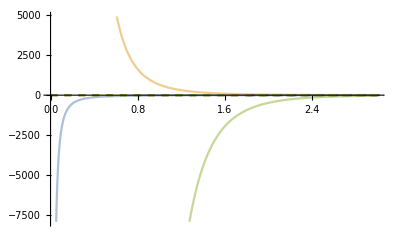

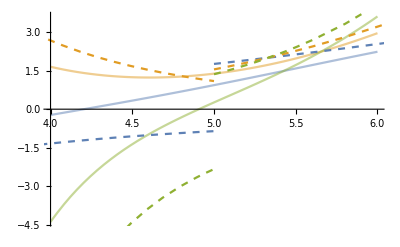

```mathematica
ϕa = 2{ ((3Ω)/16)^2,((3Ω)/16)^4,((3Ω)/16)^6};
ϕb = 2{ (-2^6/(3 Ω^2))^1 Gamma[1+1/2]/(√π),(-2^6/(3 Ω^2))^2 Gamma[2+1/2]/(√π),(-2^6/(3 Ω^2))^3 Gamma[3+1/2]/(√π)};
Show[Plot[ϕ,{Ω,0,3},PlotStyle->Opacity[0.5]],Plot[ϕb,{Ω,0,15},PlotStyle->Dashed],Plot[ϕa,{Ω,0,15},PlotStyle->Dashed]]

Show[Plot[ϕ,{Ω,4,6},PlotStyle->Opacity[0.5]],Plot[ϕb,{Ω,0,5},PlotStyle->Dashed],Plot[ϕa,{Ω,5,15},PlotStyle->Dashed]]
```

```mathematica
Binomial[2n,0](-2^7/(3*2))^n Gamma[n+1/2]/(√π)
```

((-64/3)^n Gamma[1/2+n])/(√π)

```mathematica
Integrate[ (( -I m1)^(2 n)+( -I m2)^(2 n))ⅇ^(-3/2^7(m1^2+m2^2)),{m1,-∞,∞},{m2,-∞,∞},GenerateConditions->False]
Integrate[ ⅇ^(-3/2^7 m^2),{m,-∞,∞}]^2
%%/%//Simplify
```

2^(8+7 n) 3^(-1-n) √π Cos[n π] Gamma[1/2+n]

(128 π)/3

(2^(1+7 n) 3^-n Cos[n π] Gamma[1/2+n])/(√π)

```mathematica
{Sum[Binomial[2,2l] (-2^7/(6 Ω^2))^(1-l)Gamma[1-l+1/2]/(√π),{l,0,1}],Sum[Binomial[4,2l] (-2^7/(6 Ω^2))^(2-l)Gamma[2-l+1/2]/(√π),{l,0,2}],Sum[Binomial[6,2l] (-2^7/(6 Ω^2))^(3-l)Gamma[3-l+1/2]/(√π),{l,0,3}]}
```

{1-32/(3 Ω^2),1+1024/(3 Ω^4)-64/Ω^2,1-163840/(9 Ω^6)+5120/Ω^4-160/Ω^2}

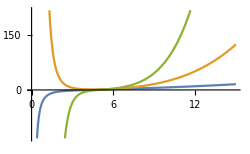

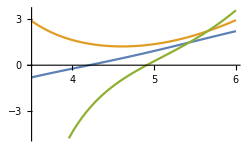

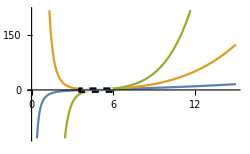

-Graphics-

```mathematica
p1=Plot[ϕ,{Ω,0,15},
AxesLabel->{MaTeX["\\Omega"],MaTeX[" \\langle \\operatorname{Tr} \\phi^{2k} \\rangle_{SU(2)}"]},ImageSize->250
]
p2=Plot[ϕ,{Ω,3.5,6},
AxesLabel->{MaTeX["\\Omega"],MaTeX[" \\langle \\operatorname{Tr} \\phi^{2k} \\rangle_{SU(2)}"]},
PlotLegends->{MaTeX[" \\langle \\operatorname{Tr} \\phi^{2} \\rangle_{SU(2)}"],MaTeX[" \\langle \\operatorname{Tr} \\phi^{4} \\rangle_{SU(2)}"],MaTeX[" \\langle \\operatorname{Tr} \\phi^{6} \\rangle_{SU(2)}"]},ImageSize->250
]
RegionPlot[3.5<x<6 && -8<y<10,{x,3,7},{y,-5,4},BoundaryStyle->{Black,Dashed},PlotStyle->{LightBlue,Opacity[0.15]},
ImageSize->250,PlotRangePadding->0,PlotRange->All,PlotPoints->80
];
GraphicsRow[{Show[p1,%],Show[p2,%]},ImageSize->Full,Spacings->{0,0},PlotRangePadding->0,Spacings->{2,2},PlotRange->All];
Show[%,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]
GraphicsRow[{p1,p2}]
```

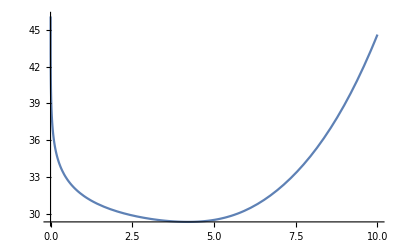

-Graphics-

```mathematica
Plot[Log[ (2^16 π^(29/2))/3 ((128 √(3 π) (4294967296+81 Ω^4 (-20480+3 Ω^4))+9 ⅇ^((3 Ω^4)/16384) π Ω^2 ((1635778560+331776 Ω^4-81 Ω^8) Erfc[(√3 Ω^2)/128]-1048576000 ⅇ^((3 Ω^4)/2048) Erfc[(3 √3 Ω^2)/128]))/(12884901888 Ω^2))+5^3 2^8 π^(31/2)ⅇ^(27/2^14 Ω^4)],{Ω,0,10},
AxesLabel->{MaTeX["\\Omega"],MaTeX["\\operatorname{log}Z_{SU(2)}(\\Omega)"]},ImageSize->400]
GraphicsRow[{%}]
```

```mathematica
vars = Table[ϕSUN[k],{k,1,5}];
ϕSUN[0]=NN;
ϕUN = Table[ NN (-2^7/(3 Ω^2))^n Gamma[n+1/2]/(√π),{n,1,5}]
Table[Sum[ Binomial[2n,2k] (-2^7/(3 NN Ω^2))^(n-k)Gamma[n-k+1/2]/(√π)ϕSUN[k]
,{k,0,n}],{n,1,5}]
Solve[%==%%,vars]//FullSimplify
```

{-(64 NN)/(3 Ω^2),(4096 NN)/(3 Ω^4),-(1310720 NN)/(9 Ω^6),(587202560 NN)/(27 Ω^8),-(37580963840 NN)/(9 Ω^10)}

{-64/(3 Ω^2)+ϕSUN[1],4096/(3 NN Ω^4)-(128 ϕSUN[1])/(NN Ω^2)+ϕSUN[2],-1310720/(9 NN^2 Ω^6)+(20480 ϕSUN[1])/(NN^2 Ω^4)-(320 ϕSUN[2])/(NN Ω^2)+ϕSUN[3],587202560/(27 NN^3 Ω^8)-(36700160 ϕSUN[1])/(9 NN^3 Ω^6)+(286720 ϕSUN[2])/(3 NN^2 Ω^4)-(1792 ϕSUN[3])/(3 NN Ω^2)+ϕSUN[4],-37580963840/(9 NN^4 Ω^10)+(2936012800 ϕSUN[1])/(3 NN^4 Ω^8)-(91750400 ϕSUN[2])/(3 NN^3 Ω^6)+(286720 ϕSUN[3])/(NN^2 Ω^4)-(960 ϕSUN[4])/(NN Ω^2)+ϕSUN[5]}

{{ϕSUN[1]→-(64 (-1+NN))/(3 Ω^2),ϕSUN[2]→(4096 (-1+NN)^2)/(3 NN Ω^4),ϕSUN[3]→-(1310720 (-1+NN)^3)/(9 NN^2 Ω^6),ϕSUN[4]→(587202560 (-1+NN)^4)/(27 NN^3 Ω^8),ϕSUN[5]→-(37580963840 (-1+NN)^5)/(9 NN^4 Ω^10)}}

```mathematica
NN=2;
Assuming[n ∈ Integers && NN ∈ Integers && NN>n,((3 Ω)/8)^(2 n)Sum[m^(2n),{m,(- NN+1)/2,(NN-1)/2}]];
Table[%,{n,1,5}]
Assuming[n ∈ Integers && NN ∈ Integers && NN>n,2((3 Ω)/16)^(2 n)];
Table[%,{n,1,5}]
ClearAll[n,NN]
```

{(9 Ω^2)/128,(81 Ω^4)/32768,(729 Ω^6)/8388608,(6561 Ω^8)/2147483648,(59049 Ω^10)/549755813888}

{(9 Ω^2)/128,(81 Ω^4)/32768,(729 Ω^6)/8388608,(6561 Ω^8)/2147483648,(59049 Ω^10)/549755813888}